## Prelim

### Creating some functions for linear transformations

```mathematica
A[r_]:={{0,-r[[3]],r[[2]]},{r[[3]],0,-r[[1]]},{-r[[2]],r[[1]],0}};
```

```mathematica
Q[rvec_,θ_]:=(1-Cos[θ])*rvec⊗rvec+Cos[θ]*IdentityMatrix[3]+Sin[θ]*A[rvec];
```

```mathematica
T[u_,c_]:=u+c;
```

```mathematica
RotateAbout[QMat_,c_,x_]:=T[QMat.T[x,-c],c];
```

```mathematica
MatrixProduct[As_]:=Module[{ret,i},
ret=IdentityMatrix[Length[As[[1]]]];
For[i=1,i≤Length[As],i++,
ret=ret.As[[i]];
];
ret
]
```

```mathematica
QRod[ω_]:=Module[{r,θ},
θ=Norm[ω];
r=If[θ>0,ω/θ,ω];
Return[If[θ>0,Q[r,θ],IdentityMatrix[3]]];
]
```

#### Worm-like chain free energy

```mathematica
Wwlc[λ_]:=kT*k*(2*λ^2+1/(1-λ)-λ)
```

```mathematica
D[Wwlc[Sqrt[x]],{x,2}]
```

k kT (1/(4 x^(3/2))-1/(4 (1-√x)^2 x^(3/2))+1/(2 (1-√x)^3 x))

```mathematica
d2Wwlcdx2=Simplify[D[Wwlc[Sqrt[x]],{x,2}]]
```

(k kT (-3+√x))/(4 (-1+√x)^3 √x)

Clearly, this is convex with respect to x^2

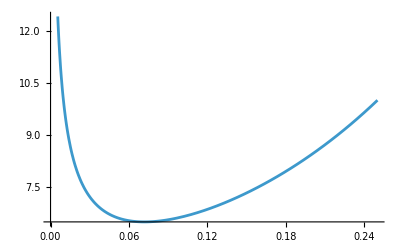

```mathematica
Plot[d2Wwlcdx2/.{k*kT->1},{x,0,0.25}]
```

Thus, Wormlike chain also should satisfy the equipartition property (i.e. it is a convex function of the stretch squared)

### Freely jointed chain (KG approximation)

```mathematica
LangInv[x_]:=3*x+x^2/5*Sin[7*x/2]+x^3/(1-x)
```

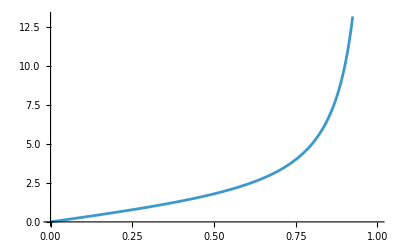

```mathematica
Plot[LangInv[x],{x,0,1}]
```

```mathematica
WLang[γ_,n_:1,kT_:1]:=Module[{β},
β=LangInv[γ];
Return[n*kT*(γ*β+Log[β*Csch[β]])];
]
```

```mathematica
N[Log[1/(4*π)]]
```

-2.53102

```mathematica
WGauss[λ_,n_:1,kT_:1]:=3/2 n*kT*λ^2
```

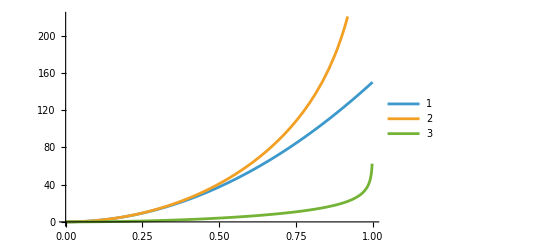

```mathematica
Plot[{WGauss[γ,100],WLang[γ,100],WLang[γ,10]},{γ,0,1},PlotLegends->Automatic]
```

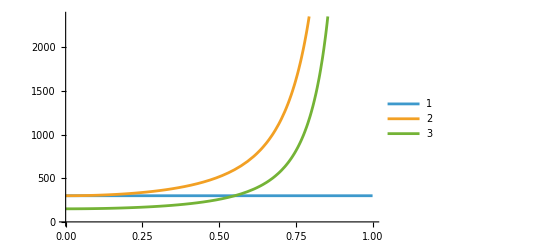

```mathematica
Plot[{D[WGauss[γ,100],{γ,2}]/.{γ->γv},D[WLang[γ,100],{γ,2}]/.{γ->γv},D[WLang[γ,50],{γ,2}]/.{γ->γv}},{γv,0,1},PlotLegends->Automatic]
```

```mathematica
frs={WGauss[γ,100]/.{γ->r/100},WGauss[γ,50]/.{γ->r/50},WLang[γ,100]/.{γ->r/100},WLang[γ,50]/.{γ->r/50}};
```

```mathematica
ers=Table[D[fr,{r,2}],{fr,frs}];
```

```mathematica
ers[[3]]=ers[[3]]/.{r->γ*100};
ers[[4]]=ers[[4]]/.{r->γ*50};
```

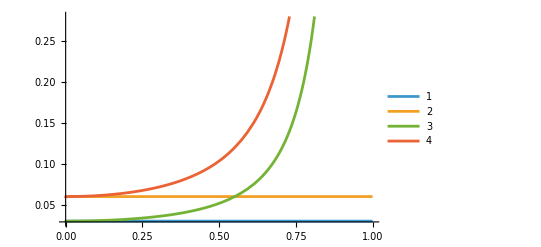

```mathematica
Plot[ers,{γ,0,1},PlotLegends->Automatic]
```

## Unification of discrete polymer network models (Section 4)

```mathematica
$Assumptions=θ∈Reals&&ϕ∈Reals&&ψ∈Reals
```

θ∈ℝ&&ϕ∈ℝ&&ψ∈ℝ

Reference end-to-end vectors for the 4-chain model

```mathematica
c4Rs=r0*{{0,0,1},{0,2*Sqrt[2]/3,-1/3},{Sqrt[2/3],-Sqrt[2]/3,-1/3},{-Sqrt[2/3],-Sqrt[2]/3,-1/3}}
```

{{0,0,r0},{0,(2 √2 r0)/3,-r0/3},{√(2/3) r0,-(√2 r0)/3,-r0/3},{-√(2/3) r0,-(√2 r0)/3,-r0/3}}

This is a generic symmetric 3x3 matrix

```mathematica
testC={{c[1,1],c[1,2],c[1,3]},{c[1,2],c[2,2],c[2,3]},{c[1,3],c[2,3],c[3,3]}};
```

This shows that the sum of the square stretch is conserved

```mathematica
Simplify[Sum[c4Rs[[j]].testC.c4Rs[[j]],{j,1,4}]]
```

4/3 r0^2 (c[1,1]+c[2,2]+c[3,3])

Reference end-to-end vectors for the 8-chain model; sum of the square stretch is conserved

```mathematica
c8Rs=r0/(√3)*ArrayReshape[Table[{(-1)^(i-1),(-1)^(j-1),(-1)^(k-1)},{i,1,2},{j,1,2},{k,1,2}],{8,3}]
```

{{r0/(√3),r0/(√3),r0/(√3)},{r0/(√3),r0/(√3),-r0/(√3)},{r0/(√3),-r0/(√3),r0/(√3)},{r0/(√3),-r0/(√3),-r0/(√3)},{-r0/(√3),r0/(√3),r0/(√3)},{-r0/(√3),r0/(√3),-r0/(√3)},{-r0/(√3),-r0/(√3),r0/(√3)},{-r0/(√3),-r0/(√3),-r0/(√3)}}

```mathematica
Simplify[Sum[c8Rs[[j]].testC.c8Rs[[j]],{j,1,8}]]
```

8/3 r0^2 (c[1,1]+c[2,2]+c[3,3])

Reference end-to-end vectors for the 3-chain model; sum of the square stretch is conserved

```mathematica
c3Rs=r0*{{1,0,0},{0,1,0},{0,0,1}}
```

{{r0,0,0},{0,r0,0},{0,0,r0}}

```mathematica
c6Rs=Catenate[{c3Rs,-c3Rs}]
```

{{r0,0,0},{0,r0,0},{0,0,r0},{-r0,0,0},{0,-r0,0},{0,0,-r0}}

```mathematica
Simplify[Sum[c3Rs[[j]].testC.c3Rs[[j]],{j,1,3}]]
```

r0^2 (c[1,1]+c[2,2]+c[3,3])

```mathematica
r0sub={r0->b*√n};
ω0=1/(√3){π/4,π/4,π/4}
```

{π/(4 √3),π/(4 √3),π/(4 √3)}

```mathematica
New3Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{},
NMinimize[{Sum[Block[{r,λ,R},
R=c3Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,3}]/3,{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]},{ωx,ωy,ωz}]
]
New3ChainLocal[F_,f_:WLang,nv_:100,bv_:1,ωv_:ω0]:=Module[{},
FindMinimum[Sum[Block[{r,λ,R},
R=c3Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,3}]/3,{ωx,ωv[[1]]},{ωy,ωv[[2]]},{ωz,ωv[[3]]}]
]
```

```mathematica
New8Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{},
NMinimize[{Sum[Block[{r,λ,R},
R=c8Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,8}]/8,{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]},{ωx,ωy,ωz}]
]
New8ChainLocal[F_,f_:WLang,nv_:100,bv_:1,ωv_:ω0]:=Module[{},
FindMinimum[Sum[Block[{r,λ,R},
R=c8Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,8}]/8,{ωx,ωv[[1]]},{ωy,ωv[[2]]},{ωz,ωv[[3]]}]
]
Standard8Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{λ},
λ=Sqrt[Tr[Transpose[F].F]/(3*nv)];
f[λ]
]
```

```mathematica
New4Chain[F_,f_:WLang,nv_:100,bv_:1]:=Module[{},
NMinimize[{Sum[Block[{r,λ,R},
R=c4Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,4}],{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]},{ωx,ωy,ωz}]
]
New4ChainLocal[F_,f_:WLang,nv_:100,bv_:1,ωv_:ω0]:=Module[{},
FindMinimum[Sum[Block[{r,λ,R},
R=c4Rs[[i]]/.r0sub;
r=N[(F.QRod[{ωx,ωy,ωz}].R)/.{n->nv,b->bv}];
λ=Norm[r]/(nv*bv);
N[f[λ]]
],{i,1,4}]/4,{ωx,ωv[[1]]},{ωy,ωv[[2]]},{ωz,ωv[[3]]}]
]
```

```mathematica
uniF[λ_]:={{λ,0,0},{0,1/Sqrt[λ],0},{0,0,1/Sqrt[λ]}}
```

```mathematica
Clear[β]
```

```mathematica
testQ4Solns={{α->-(3 π)/4,β->-ArcCos[-√(2/3)],γ->-π/2},{α->-(3 π)/4,β->-ArcCos[-√(2/3)],γ->π/6},{α->-(3 π)/4,β->-ArcCos[-√(2/3)],γ->(5 π)/6},{α->-(3 π)/4,β->ArcCos[-√(2/3)],γ->-(5 π)/6},{α->-(3 π)/4,β->ArcCos[-√(2/3)],γ->-π/6},{α->-(3 π)/4,β->ArcCos[-√(2/3)],γ->π/2},{α->-(3 π)/4,β->-ArcCos[√(2/3)],γ->-(5 π)/6},{α->-(3 π)/4,β->-ArcCos[√(2/3)],γ->-π/6},{α->-(3 π)/4,β->-ArcCos[√(2/3)],γ->π/2},{α->-(3 π)/4,β->ArcCos[√(2/3)],γ->-π/2},{α->-(3 π)/4,β->ArcCos[√(2/3)],γ->π/6},{α->-(3 π)/4,β->ArcCos[√(2/3)],γ->(5 π)/6},{α->-π/4,β->-ArcCos[-√(2/3)],γ->-π/2},{α->-π/4,β->-ArcCos[-√(2/3)],γ->π/6},{α->-π/4,β->-ArcCos[-√(2/3)],γ->(5 π)/6},{α->-π/4,β->ArcCos[-√(2/3)],γ->-(5 π)/6},{α->-π/4,β->ArcCos[-√(2/3)],γ->-π/6},{α->-π/4,β->ArcCos[-√(2/3)],γ->π/2},{α->-π/4,β->-ArcCos[√(2/3)],γ->-(5 π)/6},{α->-π/4,β->-ArcCos[√(2/3)],γ->-π/6},{α->-π/4,β->-ArcCos[√(2/3)],γ->π/2},{α->-π/4,β->ArcCos[√(2/3)],γ->-π/2},{α->-π/4,β->ArcCos[√(2/3)],γ->π/6},{α->-π/4,β->ArcCos[√(2/3)],γ->(5 π)/6},{α->π/4,β->-ArcCos[-√(2/3)],γ->-π/2},{α->π/4,β->-ArcCos[-√(2/3)],γ->π/6},{α->π/4,β->-ArcCos[-√(2/3)],γ->(5 π)/6},{α->π/4,β->ArcCos[-√(2/3)],γ->-(5 π)/6},{α->π/4,β->ArcCos[-√(2/3)],γ->-π/6},{α->π/4,β->ArcCos[-√(2/3)],γ->π/2},{α->π/4,β->-ArcCos[√(2/3)],γ->-(5 π)/6},{α->π/4,β->-ArcCos[√(2/3)],γ->-π/6},{α->π/4,β->-ArcCos[√(2/3)],γ->π/2},{α->π/4,β->ArcCos[√(2/3)],γ->-π/2},{α->π/4,β->ArcCos[√(2/3)],γ->π/6},{α->π/4,β->ArcCos[√(2/3)],γ->(5 π)/6},{α->(3 π)/4,β->-ArcCos[-√(2/3)],γ->-π/2},{α->(3 π)/4,β->-ArcCos[-√(2/3)],γ->π/6},{α->(3 π)/4,β->-ArcCos[-√(2/3)],γ->(5 π)/6},{α->(3 π)/4,β->ArcCos[-√(2/3)],γ->-(5 π)/6},{α->(3 π)/4,β->ArcCos[-√(2/3)],γ->-π/6},{α->(3 π)/4,β->ArcCos[-√(2/3)],γ->π/2},{α->(3 π)/4,β->-ArcCos[√(2/3)],γ->-(5 π)/6},{α->(3 π)/4,β->-ArcCos[√(2/3)],γ->-π/6},{α->(3 π)/4,β->-ArcCos[√(2/3)],γ->π/2},{α->(3 π)/4,β->ArcCos[√(2/3)],γ->-π/2},{α->(3 π)/4,β->ArcCos[√(2/3)],γ->π/6},{α->(3 π)/4,β->ArcCos[√(2/3)],γ->(5 π)/6}};
```

```mathematica
QGen=Q[{1,0,0},α].Q[{0,1,0},β].Q[{0,0,1},γ];
```

```mathematica
Q4=Simplify[QGen/.testQ4Solns[[3]]]
```

{{1/(√2),1/(√6),-1/(√3)},{-1/(√2),1/(√6),-1/(√3)},{0,√(2/3),1/(√3)}}

```mathematica
Manipulate[MatrixForm[Table[Simplify[(QGen/.testQ4Solns[[i]]).cp4Rs[[j]]],{j,1,4}]],{i,1,Length[testQ4Solns],1}]
```

## Linearized 4-chain model

```mathematica
cp4Rs=Table[c4Rs[[i]]/.{r0->b*√Subscript[n, i]},{i,1,4}]
```

{{0,0,b √n_1},{0,2/3 √2 b √n_2,-1/3 b √n_2},{√(2/3) b √n_3,-1/3 √2 b √n_3,-1/3 b √n_3},{-√(2/3) b √n_4,-1/3 √2 b √n_4,-1/3 b √n_4}}

```mathematica
rp4s=Table[cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]},{i,1,4}]
```

{{-xc_1,-xc_2,b √n_1-xc_3},{-xc_1,2/3 √2 b √n_2-xc_2,-1/3 b √n_2-xc_3},{√(2/3) b √n_3-xc_1,-1/3 √2 b √n_3-xc_2,-1/3 b √n_3-xc_3},{-√(2/3) b √n_4-xc_1,-1/3 √2 b √n_4-xc_2,-1/3 b √n_4-xc_3}}

Try a simple uniaxial deformation with Gaussian chains

```mathematica
FUni={{Subscript[λ, 1],0,0},{0,Subscript[λ, 2],0},{0,0,1/(Subscript[λ, 1]*Subscript[λ, 2])}};
```

```mathematica
WGauss[γ]
```

(3 γ^2)/2

```mathematica
Cases13={{Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->n,Subscript[n, 3]->n,Subscript[n, 4]->n}, {Subscript[n, 1]->n,Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->n,Subscript[n, 4]->n}, {Subscript[n, 1]->n,Subscript[n, 2]->n,Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->n}, {Subscript[n, 1]->n,Subscript[n, 2]->n,Subscript[n, 3]->n,Subscript[n, 4]->Subscript[n, a]}};
```

```mathematica
test13Solns=Simplify[{{Subscript[w, 2]->2+Subscript[w, 1]-(3 (Subscript[λ, 1]^2+Subscript[λ, 2]^2))/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[w, 3]->-1-Subscript[w, 1]+(3 Subscript[λ, 1]^2)/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[yc, 1]->(√3 b √n (-√n+√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1] Subscript[λ, 2]^2)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 2]->(√3 b √n (-√n+√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^2 Subscript[λ, 2])/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 3]->(√3 b √n (√n-√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^3 Subscript[λ, 2]^3)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4))},{Subscript[w, 2]->-2-Subscript[w, 1]+(3 (Subscript[λ, 1]^2+Subscript[λ, 2]^2))/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[w, 3]->1+Subscript[w, 1]-(3 Subscript[λ, 1]^2)/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[yc, 1]->(√3 b √n (-√n+√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1] Subscript[λ, 2]^2)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 2]->(√3 b √n (√n-√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^2 Subscript[λ, 2])/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 3]->(√3 b √n (-√n+√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^3 Subscript[λ, 2]^3)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4))},{Subscript[w, 2]->-2+Subscript[w, 1]+(3 (Subscript[λ, 1]^2+Subscript[λ, 2]^2))/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[w, 3]->-1+Subscript[w, 1]+(3 Subscript[λ, 1]^2)/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[yc, 1]->(√3 b √n (√n-√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1] Subscript[λ, 2]^2)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 2]->(√3 b √n (√n-√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^2 Subscript[λ, 2])/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 3]->(√3 b √n (√n-√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^3 Subscript[λ, 2]^3)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4))},{Subscript[w, 2]->2-Subscript[w, 1]-(3 (Subscript[λ, 1]^2+Subscript[λ, 2]^2))/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[w, 3]->1-Subscript[w, 1]-(3 Subscript[λ, 1]^2)/(Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4),Subscript[yc, 1]->(√3 b √n (√n-√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1] Subscript[λ, 2]^2)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 2]->(√3 b √n (-√n+√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^2 Subscript[λ, 2])/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4)),Subscript[yc, 3]->(√3 b √n (-√n+√Subscript[n, a]) √Subscript[n, a] Subscript[λ, 1]^3 Subscript[λ, 2]^3)/((n+3 Subscript[n, a]) (Subscript[λ, 1]^2+Subscript[λ, 2]^2+Subscript[λ, 1]^4 Subscript[λ, 2]^4))}}/.{Subscript[w, 1]->0},n∈Reals&&n>0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0]
```

{{w_2→2-(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→-1+(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→-(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→-(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))},{w_2→-2+(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→1-(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→-(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→-(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))},{w_2→-2+(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→-1+(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))},{w_2→2-(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→1-(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→-(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→-(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))}}

```mathematica
Cases22={
{Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->Subscript[n, b],Subscript[n, 4]->Subscript[n, b]},
{Subscript[n, 1]->Subscript[n, b],Subscript[n, 2]->Subscript[n, b],Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->Subscript[n, a]},
{Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->Subscript[n, b],Subscript[n, 3]->Subscript[n, b],Subscript[n, 4]->Subscript[n, a]},
{Subscript[n, 1]->Subscript[n, b],Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->Subscript[n, b]},
{Subscript[n, 1]->Subscript[n, b],Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->Subscript[n, b],Subscript[n, 4]->Subscript[n, a]},
{Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->Subscript[n, b],Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->Subscript[n, b]}
};
```

```mathematica
test22Solns=FullSimplify[{
{Subscript[w, 2]->0,Subscript[w, 3]->0,Subscript[yc, 1]->(b √Subscript[n, a] (√Subscript[n, a]-√Subscript[n, b]) √Subscript[n, b] Subscript[λ, 1])/(√3 (Subscript[n, a]+Subscript[n, b])),Subscript[yc, 2]->0,Subscript[yc, 3]->0},
{Subscript[w, 2]->0,Subscript[w, 3]->0,Subscript[yc, 1]->-(b √Subscript[n, a] (√Subscript[n, a]-√Subscript[n, b]) √Subscript[n, b] Subscript[λ, 1])/(√3 (Subscript[n, a]+Subscript[n, b])),Subscript[yc, 2]->0,Subscript[yc, 3]->0},
{Subscript[w, 1]->0,Subscript[w, 3]->0,Subscript[yc, 1]->0,Subscript[yc, 2]->(b √Subscript[n, a] (√Subscript[n, a]-√Subscript[n, b]) √Subscript[n, b] Subscript[λ, 2])/(√3 (Subscript[n, a]+Subscript[n, b])),Subscript[yc, 3]->0},
{Subscript[w, 1]->0,Subscript[w, 3]->0,Subscript[yc, 1]->0,Subscript[yc, 2]->-(b √Subscript[n, a] (√Subscript[n, a]-√Subscript[n, b]) √Subscript[n, b] Subscript[λ, 2])/(√3 (Subscript[n, a]+Subscript[n, b])),Subscript[yc, 3]->0},
{Subscript[w, 1]->0,Subscript[w, 2]->0,Subscript[yc, 1]->0,Subscript[yc, 2]->0,Subscript[yc, 3]->(b √Subscript[n, a] (√Subscript[n, a]-√Subscript[n, b]) √Subscript[n, b])/(√3 (Subscript[n, a]+Subscript[n, b]) Subscript[λ, 1] Subscript[λ, 2])},
{Subscript[w, 1]->0,Subscript[w, 2]->0,Subscript[yc, 1]->0,Subscript[yc, 2]->0,Subscript[yc, 3]->-(b √Subscript[n, a] (√Subscript[n, a]-√Subscript[n, b]) √Subscript[n, b])/(√3 (Subscript[n, a]+Subscript[n, b]) Subscript[λ, 1] Subscript[λ, 2])}
},Subscript[n, b]∈Reals&&Subscript[n, b]>0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0]
```

{{w_2→0,w_3→0,yc_1→(b n_a √n_b λ_1-b √n_a n_b λ_1)/(√3 (n_a+n_b)),yc_2→0,yc_3→0},{w_2→0,w_3→0,yc_1→(-b n_a √n_b λ_1+b √n_a n_b λ_1)/(√3 (n_a+n_b)),yc_2→0,yc_3→0},{w_1→0,w_3→0,yc_1→0,yc_2→(b n_a √n_b λ_2-b √n_a n_b λ_2)/(√3 (n_a+n_b)),yc_3→0},{w_1→0,w_3→0,yc_1→0,yc_2→(-b n_a √n_b λ_2+b √n_a n_b λ_2)/(√3 (n_a+n_b)),yc_3→0},{w_1→0,w_2→0,yc_1→0,yc_2→0,yc_3→(b n_a √n_b-b √n_a n_b)/(√3 (n_a+n_b) λ_1 λ_2)},{w_1→0,w_2→0,yc_1→0,yc_2→0,yc_3→(-b n_a √n_b+b √n_a n_b)/(√3 (n_a+n_b) λ_1 λ_2)}}

```mathematica
Qp=Simplify[(Block[{θ,r},
θ=√({Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3]}.{Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3]});
r={Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3]}/θ;
Q[r,θ]
]).(QGen/.testQ4Solns[[1]])
];
```

```mathematica
(*W13s=Table[Simplify[(Sum[3/2 kT *((FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}).(FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}))/(Subscript[n, i]*b^2),{i,1,4}]/.Join[{Subscript[ω, 1]->0,Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]-> Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3]},Cases13[[k]]])/.test13Solns[[k]],n∈Reals&&n>0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0,TimeConstraint->10],{k,1,Length[test13Solns]}]*)
W13s=Table[(Sum[3/2 kT *((FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}).(FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}))/(Subscript[n, i]*b^2),{i,1,4}]/.Join[{Subscript[ω, 1]->0,Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]-> Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3]},Cases13[[k]]])/.test13Solns[[k]],{k,1,Length[test13Solns]}];
W22s=Table[FullSimplify[(Sum[3/2 kT *((FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}).(FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}))/(Subscript[n, i]*b^2),{i,1,4}]/.Join[{Subscript[ω, 1]->Subscript[w, 1],Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]-> Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3]},Cases22[[k]]])/.test22Solns[[k]],Subscript[n, b]∈Reals&&Subscript[n, b]>0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0],{k,1,Length[test22Solns]}]
```

{kT ((1+(2 √(n_a n_b))/(n_a+n_b)) λ_1^2+2/(λ_1^2 λ_2^2)+2 λ_2^2),kT ((1+(2 √(n_a n_b))/(n_a+n_b)) λ_1^2+2/(λ_1^2 λ_2^2)+2 λ_2^2),kT (2 λ_1^2+2/(λ_1^2 λ_2^2)+(1+(2 √(n_a n_b))/(n_a+n_b)) λ_2^2),kT (2 λ_1^2+2/(λ_1^2 λ_2^2)+(1+(2 √(n_a n_b))/(n_a+n_b)) λ_2^2),kT (2 λ_1^2+(n_a+n_b+2 √(n_a n_b))/((n_a+n_b) λ_1^2 λ_2^2)+2 λ_2^2),kT (2 λ_1^2+(n_a+n_b+2 √(n_a n_b))/((n_a+n_b) λ_1^2 λ_2^2)+2 λ_2^2)}

```mathematica
(* All of the 1-3 approximations are identical! *)
```

```mathematica
Simplify[{W13s[[1]]-W13s[[2]],W13s[[1]]-W13s[[3]],W13s[[1]]-W13s[[4]]}]
```

{0,0,0}

```mathematica
(*Simplify[W13s[[1]],n∈Reals&&n>0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0,TimeConstraint->10]*)
```

```mathematica
N[W13s[[1]]/.{Subscript[λ, 1]->1,Subscript[λ, 2]->1.1,n->100,Subscript[n, a]->50,kT->1}]
```

6.02325

```mathematica
N[W22s[[1]]/.{Subscript[λ, 1]->1,Subscript[λ, 2]->1.1,Subscript[n, b]->100,Subscript[n, a]->50,kT->1}]
```

6.0157

```mathematica
(*Do[
Block[{Qp,W4Uni,z,W4UniGrad,zp,W4UniGradϵExpand,W4UniLinSoln,Acases,Bcases,w13n,W4SolnExpr,BSoln,BSolnAgg},
Print[k];

W4Uni=Sum[3/2 kT *((FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}).(FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}))/(Subscript[n, i]*b^2),{i,1,4}];
z={Subscript[ω, 1],Subscript[ω, 2],Subscript[ω, 3],Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]};
W4UniGrad=Table[D[W4Uni,z[[i]]],{i,1,6}]/.{Subscript[ω, 1]->ϵ*Subscript[w, 1],Subscript[ω, 2]->ϵ*Subscript[w, 2],Subscript[ω, 3]->ϵ*Subscript[w, 3],Subscript[xc, 1]->ϵ*Subscript[yc, 1],Subscript[xc, 2]->ϵ*Subscript[yc, 2],Subscript[xc, 3]->ϵ*Subscript[yc, 3]};
zp={Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]};
W4UniGradϵExpand=Simplify[Normal[Series[W4UniGrad,{ϵ,0,1}]]]/.{ϵ->1};
Print["Solving linear equations..."];
W4UniLinSoln=Solve[W4UniGradϵExpand=={0,0,0,0,0,0},zp];
Acases={{Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->n,Subscript[n, 3]->n,Subscript[n, 4]->n}, {Subscript[n, 1]->n,Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->n,Subscript[n, 4]->n}, {Subscript[n, 1]->n,Subscript[n, 2]->n,Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->n}, {Subscript[n, 1]->n,Subscript[n, 2]->n,Subscript[n, 3]->n,Subscript[n, 4]->Subscript[n, a]}};
w13n=FullSimplify[{W4UniLinSoln[[1]]/.Acases[[1]],W4UniLinSoln[[1]]/.Acases[[2]],W4UniLinSoln[[1]]/.Acases[[3]],W4UniLinSoln[[1]]/.Acases[[4]]}];
Print[w13n];
Print["avg A: ",Simplify[Total[Table[(({Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}/.w13n[[k]])/.Acases[[k]])/.{Subscript[w, 1]->0},{k,1,4}]]/4,Subscript[n, a]∈Reals&&n∈Reals]];
Bcases={{Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->Subscript[n, b],Subscript[n, 4]->Subscript[n, b]}, {Subscript[n, 1]->Subscript[n, b],Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->Subscript[n, b]}, {Subscript[n, 1]->Subscript[n, b],Subscript[n, 2]->Subscript[n, b],Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->Subscript[n, a]}, {Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->Subscript[n, b],Subscript[n, 3]->Subscript[n, b],Subscript[n, 4]->Subscript[n, a]}, {Subscript[n, 1]->Subscript[n, a],Subscript[n, 2]->Subscript[n, b],Subscript[n, 3]->Subscript[n, a],Subscript[n, 4]->Subscript[n, b]},{Subscript[n, 1]->Subscript[n, b],Subscript[n, 2]->Subscript[n, a],Subscript[n, 3]->Subscript[n, b],Subscript[n, 4]->Subscript[n, a]}};
(*Print[FullSimplify[{W4UniLinSoln[[1]]/.Bcases[[1]],W4UniLinSoln[[1]]/.Bcases[[2]],W4UniLinSoln[[1]]/.Bcases[[3]],W4UniLinSoln[[1]]/.Bcases[[4]],W4UniLinSoln[[1]]/.Bcases[[5]]}]];*)
W4SolnExpr={Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}/.W4UniLinSoln[[1]];
(*Print[FullSimplify[{Limit[W4SolnExpr,Bcases[[1]],Assumptions->Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0&&Subscript[n, b]∈Reals&&Subscript[n, b]>0],Limit[W4SolnExpr,Bcases[[2]],Assumptions->Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0&&Subscript[n, b]∈Reals&&Subscript[n, b]>0],Limit[W4SolnExpr,Bcases[[3]],Assumptions->Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0&&Subscript[n, b]∈Reals&&Subscript[n, b]>0],Limit[W4SolnExpr,Bcases[[4]],Assumptions->Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0&&Subscript[n, b]∈Reals&&Subscript[n, b]>0],Limit[W4SolnExpr,Bcases[[5]],Assumptions->Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0&&Subscript[n, b]∈Reals&&Subscript[n, b]>0],
Limit[W4SolnExpr,Bcases[[6]],Assumptions->Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0&&Subscript[n, a]∈Reals&&Subscript[n, a]>0&&Subscript[n, b]∈Reals&&Subscript[n, b]>0]}]];*)
BSolnAgg={0,0,0,0,0,0};
Do[
BSoln=Solve[(W4UniGradϵExpand/.Bcase)=={0,0,0,0,0,0},zp];
BSolnAgg=BSolnAgg+(({Subscript[w, 1],Subscript[w, 2],Subscript[w, 3],Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}/.Bcase)/.BSoln);
Print[Bcase, ": ",BSoln,"; ; ",FullSimplify[((W4Uni/.{Subscript[ω, 1]->Subscript[w, 1],Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]->Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3]})/.Bcase)/.BSoln]],
{Bcase,Bcases}
];
Print["avg B: ",BSolnAgg/6];
Print["---"];
],
{k,1,10}
]*)
```

## Uniaxial

## Gaussian chain

```mathematica
ω4=Simplify[Block[{θ},
θ=ArcCos[(Tr[Q4]-1)/2];
θ/(2*Sin[θ])*{Q4[[3,2]]-Q4[[2,3]],Q4[[1,3]]-Q4[[3,1]],Q4[[2,1]]-Q4[[1,2]]}
]]
```

{((1+√2) ArcCos[1/2 (-1+1/(√2)+1/(√3)+1/(√6))])/(√(6+2 √2+√3)),-ArcCos[1/2 (-1+1/(√2)+1/(√3)+1/(√6))]/(√(6+2 √2+√3)),-((3+√3) ArcCos[1/2 (-1+1/(√2)+1/(√3)+1/(√6))])/(√(6 (6+2 √2+√3)))}

```mathematica
P4ChainHat[F_,ω_,xc_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{Rs},
Rs=cp4Rs/.{Subscript[n, 1]->nsv[[1]],Subscript[n, 2]->nsv[[2]],Subscript[n, 3]->nsv[[3]],Subscript[n, 4]->nsv[[4]],b->1};
Sum[Block[{r,λ,R},
R=Rs[[i]];
r=N[F.(QRod[ω]).R-(QRod[ω]).xc];
λ=(√(r.r))/(nsv[[i]]*bv);
N[f[λ,nsv[[i]]]]
],{i,1,4}]
]
```

```mathematica
FUnif[λ_]:=N[{{λ,0,0},{0,1/√λ,0},{0,0,1/√λ}}]
```

```mathematica
FUnif[2.0]
```

{{2.,0.,0.},{0.,0.707107,0.},{0.,0.,0.707107}}

```mathematica
P4ChainHat[FUnif[3],{π/8,0,0},{1.0,0,0},WGauss,{1500,100,100,100}]
```

19.3793

```mathematica
NMinimize[{P4ChainHat[FUnif[1.1],{ωx,ωy,ωz},{xc1,xc2,xc3},WGauss,{100,100,100,100},1],{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]&&{xc1,xc2,xc3}∈Ball[{0,0,0},100*1]},{ωx,ωy,ωz,xc1,xc2,xc3}]
```

{6.05636,{ωx→1.13993,ωy→-0.483008,ωz→-2.0015,xc1→-2.60679×10^-8,xc2→-2.05264×10^-8,xc3→-1.70712×10^-7}}

```mathematica
P4Chain[F_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{nmax},
nmax=Max[nsv];
NMinimize[{P4ChainHat[F,{ωx,ωy,ωz},{xc1,xc2,xc3},f,nsv,bv],{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]&&{xc1,xc2,xc3}∈Ball[{0,0,0},nmax*bv]},{ωx,ωy,ωz,xc1,xc2,xc3}]
]
P4ChainLocal[F_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{},
FindMinimum[{P4ChainHat[F,{ωx,ωy,ωz},{xc1,xc2,xc3},f,nsv,bv],ωx^2+ωy^2+ωz^2<=4*π^2},{ωx,ω4[[1]]},{ωy,ω4[[2]]},{ωz,ω4[[3]]},{xc1,0},{xc2,0},{xc3,0}]
]
```

```mathematica
cp4Rs
```

{{0,0,b √n_1},{0,2/3 √2 b √n_2,-1/3 b √n_2},{√(2/3) b √n_3,-1/3 √2 b √n_3,-1/3 b √n_3},{-√(2/3) b √n_4,-1/3 √2 b √n_4,-1/3 b √n_4}}

```mathematica
P4ChainLocal[FUnif[1.1],WLang,{30,100,100,100}]
```

{5.88395,{ωx→0.168264,ωy→-4.7051,ωz→0.168263,xc1→-2.90551×10^-7,xc2→-1.799×10^-8,xc3→1.45274}}

```mathematica
shearF[s_]:={{1,0,s},{0,1,0},{0,0,1}};
```

```mathematica
P4ChainLocal[FUnif[1.5],WLang,{10,100,100,100}]
```

{5.98252,{ωx→0.508438,ωy→-1.51034,ωz→-0.508438,xc1→-6.21365×10^-9,xc2→6.54727×10^-9,xc3→2.53483}}

```mathematica
P4ChainLocal[FUnif[1.1],WGauss,{10,10,100,100}]
```

{5.54206,{ωx→0.0764889,ωy→0.968571,ωz→-1.23728,xc1→5.61159×10^-9,xc2→1.01931,xc3→0.720759}}

```mathematica
P4Chain[FUnif[1.1],WGauss,{10,10,100,100}]
```

{5.54206,{ωx→2.11954,ωy→1.84963,ωz→1.05537,xc1→-1.54706×10^-8,xc2→1.01931,xc3→0.720759}}

```mathematica
P4UniTestNum=Block[{nAvg,n1,n2},
nAvg=100;
n1=(4*nAvg)/40;
n2=(4*nAvg-n1)/3;
Table[{λ,P4Chain[FUnif[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.5,2.0,0.1}]
]
```

{{0.5,{7.22708,{ωx→2.47314,ωy→0.122088,ωz→-0.0422226,xc1→4.89658×10^-8,xc2→-4.20582×10^-8,xc3→2.62583}}},{0.6,{6.3259,{ωx→2.28981,ωy→-5.5562,ωz→-1.83408,xc1→-1.19759×10^-7,xc2→-4.77858×10^-8,xc3→2.39704}}},{0.7,{5.78506,{ωx→3.19661,ωy→1.76052,ωz→-5.11475,xc1→-1.17945×10^-8,xc2→-1.46352×10^-7,xc3→2.21923}}},{0.8,{5.48443,{ωx→-0.151292,ωy→-2.81364,ωz→-1.28521,xc1→1.54726×10^-9,xc2→4.26751×10^-8,xc3→2.0759}}},{0.9,{5.35727,{ωx→4.4431,ωy→0.482488,ωz→0.387696,xc1→-5.48736×10^-8,xc2→7.80519×10^-9,xc3→1.95718}}},{1.,{5.36354,{ωx→3.63847,ωy→-0.445383,ωz→-1.86331,xc1→-6.20856×10^-8,xc2→4.87168×10^-8,xc3→1.85674}}},{1.1,{5.28625,{ωx→1.91739,ωy→-3.5751,ωz→1.91739,xc1→5.98439×10^-8,xc2→-4.35446×10^-8,xc3→2.04242}}},{1.2,{5.29683,{ωx→2.00566,ωy→-3.43591,ωz→2.00565,xc1→-1.66418×10^-8,xc2→-5.52724×10^-8,xc3→2.22809}}},{1.3,{5.38131,{ωx→2.0528,ωy→-3.35475,ωz→2.0528,xc1→-3.7874×10^-8,xc2→-3.66877×10^-8,xc3→2.41376}}},{1.4,{5.52968,{ωx→2.09123,ωy→-3.28451,ωz→2.09123,xc1→-1.23832×10^-7,xc2→1.85936×10^-8,xc3→2.59944}}},{1.5,{5.73463,{ωx→2.11313,ωy→-3.24267,ωz→2.11313,xc1→6.12812×10^-8,xc2→-4.36207×10^-8,xc3→2.78511}}},{1.6,{5.99066,{ωx→2.49094,ωy→-2.0397,ωz→2.49094,xc1→-3.15367×10^-8,xc2→1.09365×10^-7,xc3→2.97079}}},{1.7,{6.29357,{ωx→2.49492,ωy→-2.01072,ωz→2.49492,xc1→-1.49723×10^-7,xc2→-6.18682×10^-8,xc3→3.15646}}},{1.8,{6.64009,{ωx→2.49948,ωy→-1.97543,ωz→2.49948,xc1→-2.04632×10^-7,xc2→6.46137×10^-8,xc3→3.34213}}},{1.9,{7.02765,{ωx→2.49791,ωy→-0.989687,ωz→2.49791,xc1→2.50063×10^-7,xc2→-4.87327×10^-8,xc3→3.52781}}},{2.,{7.45416,{ωx→-1.52287,ωy→-4.05142,ωz→-1.52287,xc1→1.11188×10^-7,xc2→2.17999×10^-7,xc3→3.71348}}}}

```mathematica
Table[N[W13s[[k]]/.{kT->1,Subscript[n, a]->10,n->130,Subscript[λ, 1]->1.8,Subscript[λ, 2]->1/√1.8}],{k,1,4}]
```

{8.35254,8.35254,8.35254,8.35254}

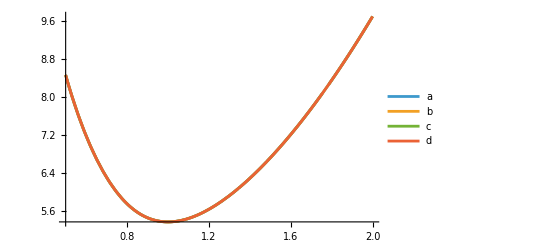

```mathematica
Block[{series},
series=Table[W13s[[k]]/.{kT->1,Subscript[n, a]->10,n->130,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{k,1,4}];
Plot[series,{λ,0.5,2.0},PlotLegends->{"a","b","c","d"}]
]
```

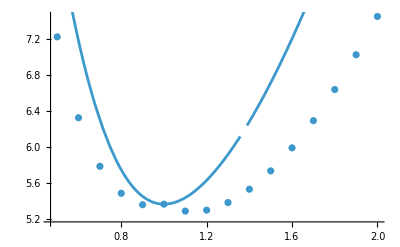

```mathematica
Show[{ListPlot[Table[{P4UniTestNum[[i,1]],P4UniTestNum[[i,2,1]]},{i,1,Length[P4UniTestNum]}]],Plot[W13s[[1]]/.{kT->1,Subscript[n, a]->10,n->130,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{λ,0.5,2.0},MaxRecursion->5]}]
```

```mathematica
P4UniTestNum2=Block[{nAvg,n1,n2},
nAvg=100;
n1=(4*nAvg)/10;
n2=(4*nAvg-n1)/3;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[FUnif[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.5,2.0,0.1}]
]
```

100, 40, 120

{{0.5,{8.23205,{ωx→0.733555,ωy→-1.95708,ωz→-3.1071,xc1→-7.97901×10^-8,xc2→1.98743×10^-7,xc3→1.89015}}},{0.6,{7.16338,{ωx→0.416719,ωy→-1.84979,ωz→-2.96159,xc1→8.93025×10^-7,xc2→2.8088×10^-7,xc3→1.72546}}},{0.7,{6.50289,{ωx→4.26219,ωy→2.35365,ωz→-3.97146,xc1→2.02831×10^-8,xc2→3.31398×10^-8,xc3→1.59747}}},{0.8,{6.11253,{ωx→2.92085,ωy→0.919162,ωz→-5.48654,xc1→2.29599×10^-7,xc2→5.47876×10^-8,xc3→1.49429}}},{0.9,{5.91558,{ωx→0.419099,ωy→-2.3322,ωz→-2.43517,xc1→-3.52194×10^-8,xc2→8.55167×10^-8,xc3→1.40883}}},{1.,{5.86603,{ωx→0.431355,ωy→-3.83189,ωz→-3.406,xc1→2.43445×10^-8,xc2→-5.85678×10^-8,xc3→1.33654}}},{1.1,{5.89425,{ωx→-1.05314,ωy→-4.41401,ωz→-1.05313,xc1→-1.19901×10^-8,xc2→2.83602×10^-7,xc3→1.47019}}},{1.2,{6.02041,{ωx→-1.03657,ωy→-4.42375,ωz→-1.03657,xc1→-2.90608×10^-9,xc2→-1.89654×10^-8,xc3→1.60384}}},{1.3,{6.23051,{ωx→1.64172,ωy→-3.92834,ωz→1.64171,xc1→1.18265×10^-7,xc2→-3.37835×10^-8,xc3→1.7375}}},{1.4,{6.51455,{ωx→1.57258,ωy→-4.00176,ωz→1.57258,xc1→-1.52805×10^-7,xc2→-2.77805×10^-7,xc3→1.87115}}},{1.5,{6.86522,{ωx→0.373833,ωy→-4.67625,ωz→0.373834,xc1→-8.92808×10^-8,xc2→7.67653×10^-8,xc3→2.0048}}},{1.6,{7.27703,{ωx→0.410732,ωy→-4.66871,ωz→0.410732,xc1→-2.06838×10^-7,xc2→1.39952×10^-7,xc3→2.13846}}},{1.7,{7.74575,{ωx→1.49293,ωy→-4.08014,ωz→1.49293,xc1→-7.62808×10^-8,xc2→3.70577×10^-7,xc3→2.27211}}},{1.8,{8.26814,{ωx→-0.880816,ωy→-4.5066,ωz→-0.880817,xc1→2.86521×10^-7,xc2→-2.37579×10^-8,xc3→2.40576}}},{1.9,{8.84161,{ωx→-1.12628,ωy→-4.36872,ωz→-1.12628,xc1→1.40818×10^-7,xc2→-2.38818×10^-7,xc3→2.53942}}},{2.,{9.4641,{ωx→-1.10763,ωy→-4.38062,ωz→-1.10763,xc1→2.21953×10^-7,xc2→-2.28904×10^-7,xc3→2.67307}}}}

```mathematica
P4UniTestNum3=Block[{nAvg,n1,n2},
nAvg=100;
n1=70;
n2=(4*nAvg-n1)/3;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[FUnif[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.5,2.0,0.1}]
]
```

100, 70, 110

{{0.5,{8.45781,{ωx→1.50994,ωy→4.74184,ωz→-3.83582,xc1→-1.52571×10^-7,xc2→-8.30453×10^-8,xc3→0.822718}}},{0.6,{7.3515,{ωx→2.60711,ωy→-3.45047,ωz→-4.55803,xc1→-8.76723×10^-7,xc2→-1.95606×10^-7,xc3→0.751035}}},{0.7,{6.66415,{ωx→2.60714,ωy→-3.45047,ωz→-4.55802,xc1→-1.78858×10^-7,xc2→-1.30648×10^-7,xc3→0.695323}}},{0.8,{6.25363,{ωx→4.46115,ωy→-2.32508,ωz→-3.76438,xc1→2.32411×10^-7,xc2→-7.51414×10^-8,xc3→0.650416}}},{0.9,{6.041,{ωx→3.25379,ωy→-1.02294,ωz→-4.34343,xc1→5.67861×10^-7,xc2→-3.95064×10^-7,xc3→0.613218}}},{1.,{5.9789,{ωx→2.13956,ωy→-0.546343,ωz→-4.06208,xc1→-1.25773×10^-7,xc2→-2.63359×10^-7,xc3→0.58175}}},{1.1,{6.03084,{ωx→2.39121,ωy→0.467653,ωz→-2.39122,xc1→4.35511×10^-7,xc2→2.4927×10^-7,xc3→0.639924}}},{1.2,{6.18295,{ωx→2.30463,ωy→0.202626,ωz→-2.30463,xc1→-9.4549×10^-8,xc2→4.27896×10^-7,xc3→0.698099}}},{1.3,{6.42127,{ωx→2.18168,ωy→-0.0849824,ωz→-2.18169,xc1→3.48573×10^-7,xc2→-1.07501×10^-6,xc3→0.756274}}},{1.4,{6.73579,{ωx→-2.48642,ωy→-2.07077,ωz→-2.48642,xc1→-2.16716×10^-7,xc2→-8.67911×10^-8,xc3→0.814449}}},{1.5,{7.1192,{ωx→-1.90677,ωy→-3.59084,ωz→-1.90677,xc1→-3.41501×10^-8,xc2→-2.65006×10^-7,xc3→0.872624}}},{1.6,{7.56599,{ωx→-1.90488,ωy→-3.59362,ωz→-1.90488,xc1→6.4523×10^-7,xc2→4.41403×10^-7,xc3→0.9308}}},{1.7,{8.07197,{ωx→2.20901,ωy→-0.027284,ωz→-2.20901,xc1→3.70016×10^-7,xc2→-7.8665×10^-8,xc3→0.988974}}},{1.8,{8.63387,{ωx→-1.09834,ωy→-4.38646,ωz→-1.09835,xc1→-6.72689×10^-7,xc2→-1.82461×10^-7,xc3→1.04715}}},{1.9,{9.2491,{ωx→-1.09274,ωy→-4.38995,ωz→-1.09274,xc1→2.05758×10^-7,xc2→1.72702×10^-7,xc3→1.10532}}},{2.,{9.91561,{ωx→-1.09596,ωy→-4.38795,ωz→-1.09596,xc1→9.24266×10^-7,xc2→-6.95996×10^-7,xc3→1.1635}}}}

```mathematica
(*Export["WUni1_1-3_Num.csv",Table[{P4UniTestNum2[[i,1]],P4UniTestNum2[[i,2,1]],P4UniTestNum3[[i,2,1]]},{i,1,Length[P4UniTestNum2]}]]*)
```

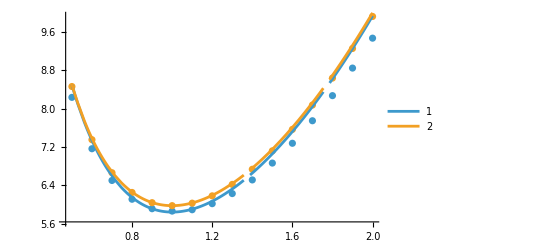

```mathematica
Show[{ListPlot[{Table[{P4UniTestNum2[[i,1]],P4UniTestNum2[[i,2,1]]},{i,1,Length[P4UniTestNum2]}],Table[{P4UniTestNum3[[i,1]],P4UniTestNum3[[i,2,1]]},{i,1,Length[P4UniTestNum3]}]}],Plot[{W13s[[1]]/.{kT->1,Subscript[n, a]->40,n->130,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},W13s[[1]]/.{kT->1,Subscript[n, a]->70,n->110,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ}},{λ,0.5,2.0},PlotLegends->Automatic]}]
```

```mathematica
(*Plot[{W4Uni1/.{kT->1,Subscript[n, 1]->10,n->130,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{W4Uni1/.{kT->1,Subscript[n, 1]->40,n->120,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ}},{W4Uni1/.{kT->1,Subscript[n, 1]->70,n->110,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{W4Uni1/.{kT->1,Subscript[n, 1]->100,n->100,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{W4Uni1/.{kT->1,Subscript[n, 1]->130,n->90,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ}}}},{W4Uni1/.{kT->1,Subscript[n, 1]->250,n->50,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ}}},{λ,0.75,1.5},PlotLegends->{"n_1=10","n_1=40","n_1=70","n_1=100","n_1=130","n_1=250"},AxesLabel->{λ,W}]*)
```

```mathematica
W13expr=W13s[[1]]/.{Subscript[λ, 1]->λa,Subscript[λ, 2]->λb};
```

```mathematica
(*Σ4=Simplify[D[W13expr,λa],TimeConstraint->10]*)
```

```mathematica
Σ4Uni=FullSimplify[D[W13s[[1]]/.{Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},λ]]
```

1/(√n λ^2 (1+2 λ^3)^3 √n_a (n+3 n_a))kT (3 √n (-4-17 λ^3-21 λ^6+10 λ^9+32 λ^12) n_a^(3/2)+9 n λ^3 ((-2-2 λ^3+4 λ^6) Cos[(√2 (-1+λ^3))/(1+2 λ^3)]+9 √2 λ^3 Sin[(√2 (-1+λ^3))/(1+2 λ^3)]) √(n n_a)+9 λ^3 n_a (2 n (-1-λ^3+2 λ^6)+((-2-2 λ^3+4 λ^6) Cos[(√2 (-1+λ^3))/(1+2 λ^3)]+9 √2 λ^3 Sin[(√2 (-1+λ^3))/(1+2 λ^3)]) √(n n_a))+√n √n_a (n (-4-11 λ^3-15 λ^6-2 λ^9+32 λ^12)-18 λ^3 ((-2-2 λ^3+4 λ^6) Cos[(√2 (-1+λ^3))/(1+2 λ^3)]+9 √2 λ^3 Sin[(√2 (-1+λ^3))/(1+2 λ^3)]) √(n n_a)))

```mathematica
Simplify[Σ4Uni]
```

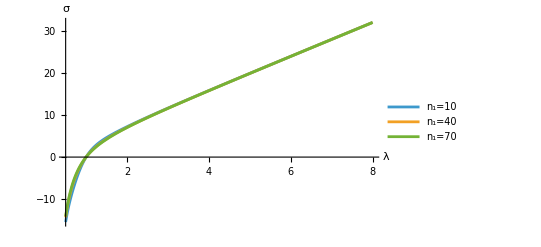

```mathematica
Plot[{Σ4Uni/.{kT->1,Subscript[n, a]->10,n->130},{Σ4Uni/.{kT->1,Subscript[n, a]->40,n->120}},{Σ4Uni/.{kT->1,Subscript[n, a]->70,n->110}}},{λ,0.5,8.0},PlotLegends->{"n_1=10","n_1=40","n_1=70"},AxesLabel->{λ,σ}]
```

```mathematica
E4Uni=FullSimplify[D[W13s[[1]]/.{Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{λ,2}]]
```

1/(√n λ^3 (1+2 λ^3)^5 √n_a (n+3 n_a))kT (3 √n (1+2 λ^3)^2 (8+55 λ^3+78 λ^6+124 λ^9+32 λ^12) n_a^(3/2)-18 n λ^3 ((1-10 λ^3-129 λ^6-40 λ^9+16 λ^12) Cos[(√2 (-1+λ^3))/(1+2 λ^3)]+27 √2 λ^3 (-1+4 λ^6) Sin[(√2 (-1+λ^3))/(1+2 λ^3)]) √(n n_a)-18 λ^3 n_a (n (1+2 λ^3)^2 (1-14 λ^3+4 λ^6)+((1-10 λ^3-129 λ^6-40 λ^9+16 λ^12) Cos[(√2 (-1+λ^3))/(1+2 λ^3)]+27 √2 λ^3 (-1+4 λ^6) Sin[(√2 (-1+λ^3))/(1+2 λ^3)]) √(n n_a))+√n √n_a (n (1+2 λ^3)^2 (8+61 λ^3-6 λ^6+148 λ^9+32 λ^12)+36 λ^3 ((1-10 λ^3-129 λ^6-40 λ^9+16 λ^12) Cos[(√2 (-1+λ^3))/(1+2 λ^3)]+27 √2 λ^3 (-1+4 λ^6) Sin[(√2 (-1+λ^3))/(1+2 λ^3)]) √(n n_a)))

```mathematica
E4Uni0=Simplify[E4Uni/.{λ->1}]
```

(3 kT (11 √n n_a^(3/2)+4 n √(n n_a)+√n √n_a (3 n-8 √(n n_a))+2 n_a (n+2 √(n n_a))))/(√n √n_a (n+3 n_a))

```mathematica
E4Uni0a=Simplify[E4Uni0/.{Subscript[n, a]->4*navg-3*n}]
```

(3 kT (11 √n (-3 n+4 navg)^(3/2)+4 n √(n (-3 n+4 navg))+√n √(-3 n+4 navg) (3 n-8 √(n (-3 n+4 navg)))+2 (-3 n+4 navg) (n+2 √(n (-3 n+4 navg)))))/(√n √(-3 n+4 navg) (-8 n+12 navg))

```mathematica
Solve[Simplify[D[E4Uni0a,n]]==0,n]
```

Solve::nongen: There may be values of the parameters for which some or all solutions are not valid.

{{n→navg},{n→(9 navg)/7}}

```mathematica
Simplify[D[E4Uni0a,{n,2}]]/.{n->navg}
```

-1/navg^7 6 kT √(navg^2) (-12 navg^4-27 navg^3 √(navg^2)+navg^3 (96 navg-15 √(navg^2))+4 navg^3 (36 navg+√(navg^2))-3 navg^3 (56 navg+√(navg^2))+2 navg^3 (-32 navg+21 √(navg^2)))

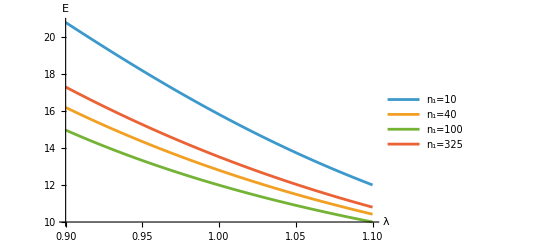

```mathematica
Plot[{E4Uni/.{kT->1,Subscript[n, a]->10,n->130},{E4Uni/.{kT->1,Subscript[n, a]->40,n->120}},{E4Uni/.{kT->1,Subscript[n, a]->100,n->100}},{E4Uni/.{kT->1,Subscript[n, a]->325,n->25}}},{λ,0.9,1.1},PlotLegends->{"n_1=10","n_1=40","n_1=100","n_1=325"},AxesLabel->{λ,Ε}]
```

```mathematica
Export["EUni_Gauss_Approx.csv",Table[{λv,E4Uni/.{kT->1,Subscript[n, a]->10,n->130,λ->λv},E4Uni/.{kT->1,Subscript[n, a]->40,n->120,λ->λv},E4Uni/.{kT->1,Subscript[n, a]->100,n->100,λ->λv},E4Uni/.{kT->1,Subscript[n, a]->325,n->25,λ->λv}},{λv,0.5,1.35,0.0125}]]
```

EUni_Gauss_Approx.csv

```mathematica
P4UniTestNum4=Block[{nAvg,n1,n2},
nAvg=100;
n1=50;
n2=(4*nAvg-2*n1)/2;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[FUnif[λ],WGauss,{n1,n1,n2,n2}]},{λ,0.5,2.0,0.1}]
];
P4UniTestNum5=Block[{nAvg,n1,n2},
nAvg=100;
n1=80;
n2=(4*nAvg-2*n1)/2;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[FUnif[λ],WGauss,{n1,n1,n2,n2}]},{λ,0.5,2.0,0.1}]
];
```

100, 50, 150

100, 80, 120

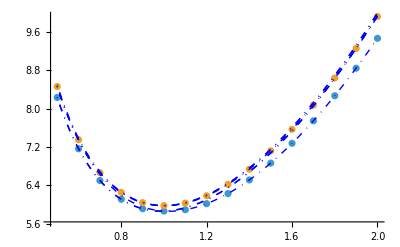

```mathematica
Block[{expr1,expr2},
expr1=Table[W22s[[k]]/.{kT->1,Subscript[n, a]->50,Subscript[n, b]->150,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{k,{1,3,5}}];
expr2=Table[W22s[[k]]/.{kT->1,Subscript[n, a]->80,Subscript[n, b]->120,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{k,{1,3,5}}];
Show[{ListPlot[{Table[{P4UniTestNum4[[i,1]],P4UniTestNum4[[i,2,1]]},{i,1,Length[P4UniTestNum4]}],Table[{P4UniTestNum5[[i,1]],P4UniTestNum5[[i,2,1]]},{i,1,Length[P4UniTestNum5]}]}],Plot[Join[expr1,expr2],{λ,0.5,2.0},PlotStyle->{Orange,Thick,Dashed,DotDashed,Blue,Thick,Dashed,DotDashed}]}]
]
```

```mathematica
W22s
```

{kT ((1+(2 √(n_a n_b))/(n_a+n_b)) λ_1^2+2/(λ_1^2 λ_2^2)+2 λ_2^2),kT ((1+(2 √(n_a n_b))/(n_a+n_b)) λ_1^2+2/(λ_1^2 λ_2^2)+2 λ_2^2),kT (2 λ_1^2+2/(λ_1^2 λ_2^2)+(1+(2 √(n_a n_b))/(n_a+n_b)) λ_2^2),kT (2 λ_1^2+2/(λ_1^2 λ_2^2)+(1+(2 √(n_a n_b))/(n_a+n_b)) λ_2^2),kT (2 λ_1^2+(n_a+n_b+2 √(n_a n_b))/((n_a+n_b) λ_1^2 λ_2^2)+2 λ_2^2),kT (2 λ_1^2+(n_a+n_b+2 √(n_a n_b))/((n_a+n_b) λ_1^2 λ_2^2)+2 λ_2^2)}

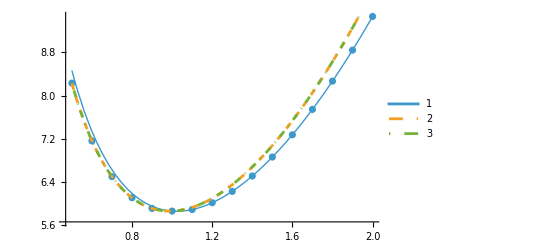

```mathematica
Block[{expr1,expr2},
expr1=Table[W22s[[k]]/.{kT->1,Subscript[n, a]->50,Subscript[n, b]->150,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{k,{1,3,5}}];
(*expr2=Table[W22/.{kT->1,Subscript[n, a]->80,Subscript[n, b]->120,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{W22,W22s}];*)
Show[{ListPlot[Table[{P4UniTestNum4[[i,1]],P4UniTestNum4[[i,2,1]]},{i,1,Length[P4UniTestNum4]}]],Plot[expr1,{λ,0.5,2.0},PlotLegends->{"1","2","3"},PlotStyle->{Thick,Dashed,DotDashed}]}]
]
```

```mathematica
P4UniTestNum6=Block[{nAvg,n1,n2},
nAvg=100;
n1=25;
n2=(4*nAvg-2*n1)/2;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[FUnif[λ],WGauss,{n1,n1,n2,n2}]},{λ,0.5,2.0,0.1}]
];
```

100, 25, 175

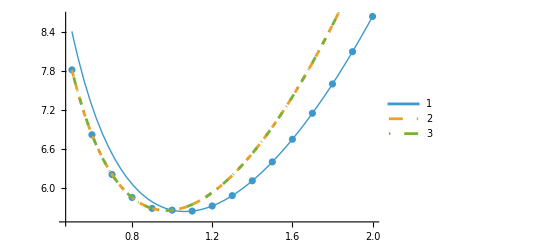

```mathematica
Block[{expr1},
expr1=Table[W22s[[k]]/.{kT->1,Subscript[n, a]->25,Subscript[n, b]->175,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{k,{1,3,5}}];
(*expr2=Table[W22/.{kT->1,Subscript[n, a]->80,Subscript[n, b]->120,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{W22,W22s}];*)
Show[{ListPlot[Table[{P4UniTestNum6[[i,1]],P4UniTestNum6[[i,2,1]]},{i,1,Length[P4UniTestNum4]}]],Plot[expr1,{λ,0.5,2.0},PlotLegends->{"1","2","3"},PlotStyle->{Thick,Dashed,DotDashed}]}]
]
```

```mathematica
cases={
{10,130,130,130},
{40,120,120,120},
{70,110,110,110},
{100,100,100,100},
{130,90,90,90},
{190,70,70,70},
{250,50,50,50},
{25,25,175,175},
{50,50,150,150},
{75,75,125,125}
};
```

```mathematica
Export["chain-4_cases.csv",cases]
```

chain-4_cases.csv

```mathematica
Export["WUni_Gauss_Num.csv",Table[Catenate[{ {λ}, Table[P4ChainLocal[FUnif[λ],WGauss,case][[1]],{case,cases}] }],{λ,0.5,2.0,0.05}]]
```

WUni_Gauss_Num.csv

```mathematica
P4ChainLocal[FUnif[1.1],WGauss,cases[[1]]]
```

{5.28625,{ωx→-0.36684,ωy→1.53949,ωz→-0.36684,xc1→3.85977×10^-9,xc2→4.5849×10^-9,xc3→2.04242}}

```mathematica
ycMags=Table[FullSimplify[(√(Subscript[yc, 1]^2+Subscript[yc, 2]^2+Subscript[yc, 3]^2))/.test13Soln],{test13Soln,test13Solns}]
```

{√3 √((b^2 n (√n-√n_a)^2 n_a λ_1^2 λ_2^2)/((n+3 n_a)^2 (λ_1^2+λ_2^2+λ_1^4 λ_2^4))),√3 √((b^2 n (√n-√n_a)^2 n_a λ_1^2 λ_2^2)/((n+3 n_a)^2 (λ_1^2+λ_2^2+λ_1^4 λ_2^4))),√3 √((b^2 n (√n-√n_a)^2 n_a λ_1^2 λ_2^2)/((n+3 n_a)^2 (λ_1^2+λ_2^2+λ_1^4 λ_2^4))),√3 √((b^2 n (√n-√n_a)^2 n_a λ_1^2 λ_2^2)/((n+3 n_a)^2 (λ_1^2+λ_2^2+λ_1^4 λ_2^4)))}

```mathematica
wMags=Table[FullSimplify[(√((0)^2+Subscript[w, 2]^2+Subscript[w, 3]^2))/.test13Soln],{test13Soln,test13Solns}]
```

{√(5-(3 (4 λ_1^2 λ_2^2+(1+6 λ_1^6) λ_2^4+4 λ_1^4 λ_2^6))/((λ_1^2+λ_2^2+λ_1^4 λ_2^4)^2)),√(5-(3 (4 λ_1^2 λ_2^2+(1+6 λ_1^6) λ_2^4+4 λ_1^4 λ_2^6))/((λ_1^2+λ_2^2+λ_1^4 λ_2^4)^2)),√(5-(3 (4 λ_1^2 λ_2^2+(1+6 λ_1^6) λ_2^4+4 λ_1^4 λ_2^6))/((λ_1^2+λ_2^2+λ_1^4 λ_2^4)^2)),√(5-(3 (4 λ_1^2 λ_2^2+(1+6 λ_1^6) λ_2^4+4 λ_1^4 λ_2^6))/((λ_1^2+λ_2^2+λ_1^4 λ_2^4)^2))}

```mathematica
(*idx=1;
Do[
Print[case];
Export["WUni_Gauss_NumSoln_case-"<>ToString[idx]<>".csv",Table[Catenate[{ {λ}, 
Block[{caseSoln,Qcase,xp},
caseSoln=P4ChainLocal[FUnif[λ],WGauss,case];
Qcase=QRod[{ωx,ωy,ωz}/.caseSoln[[2]]];
xp=(Transpose[Qcase].{xc1,xc2,xc3})/.caseSoln[[2]];
{caseSoln[[1]],ωx,ωy,ωz,xc1,xc2,xc3,xp[[1]],xp[[2]],xp[[3]]}/.caseSoln[[2]]
]
}],{λ,0.5,2.0,0.05}]];
idx+=1,
{case, cases}
]*)
```

{10,130,130,130}

{40,120,120,120}

{70,110,110,110}

{100,100,100,100}

{130,90,90,90}

{190,70,70,70}

{250,50,50,50}

{25,25,175,175}

{50,50,150,150}

{75,75,125,125}

```mathematica
W22s
```

{kT ((1+(2 √(n_a n_b))/(n_a+n_b)) λ_1^2+2/(λ_1^2 λ_2^2)+2 λ_2^2),kT ((1+(2 √(n_a n_b))/(n_a+n_b)) λ_1^2+2/(λ_1^2 λ_2^2)+2 λ_2^2),kT (2 λ_1^2+2/(λ_1^2 λ_2^2)+(1+(2 √(n_a n_b))/(n_a+n_b)) λ_2^2),kT (2 λ_1^2+2/(λ_1^2 λ_2^2)+(1+(2 √(n_a n_b))/(n_a+n_b)) λ_2^2),kT (2 λ_1^2+(n_a+n_b+2 √(n_a n_b))/((n_a+n_b) λ_1^2 λ_2^2)+2 λ_2^2),kT (2 λ_1^2+(n_a+n_b+2 √(n_a n_b))/((n_a+n_b) λ_1^2 λ_2^2)+2 λ_2^2)}

```mathematica
W13sub=W13s[[1]]/.{Subscript[λ, 1]->λa,Subscript[λ, 2]->λb,kT->1,b->1};
W22sub=Table[W22s[[k]],{k,{1,3,5}}]/.{Subscript[λ, 1]->λa,Subscript[λ, 2]->λb,kT->1}
```

{2/(λa^2 λb^2)+2 λb^2+λa^2 (1+(2 √(n_a n_b))/(n_a+n_b)),2 λa^2+2/(λa^2 λb^2)+λb^2 (1+(2 √(n_a n_b))/(n_a+n_b)),2 λa^2+2 λb^2+(n_a+n_b+2 √(n_a n_b))/(λa^2 λb^2 (n_a+n_b))}

```mathematica
N[W22sub[[1]]/.{λa->1.1,λb->1/√1.1,Subscript[n, a]->cases[[8]][[1]],Subscript[n, b]->cases[[8]][[3]]}]
```

5.6467

```mathematica
Export["WUni_Gauss_Approx.csv",Table[Catenate[{ {λ}, Table[If[case=={100,100,100,100},
P4Chain[FUnif[λ],WGauss,case][[1]],
If[case[[1]]==case[[2]],
If[λ>=1,N[W22sub[[1]]/.{λa->λ,λb->1/√λ,Subscript[n, a]->case[[1]],Subscript[n, b]->case[[3]]}],N[W22sub[[2]]/.{λa->λ,λb->1/√λ,Subscript[n, a]->case[[1]],Subscript[n, b]->case[[3]]}]],
N[W13sub/.{λa->λ,λb->1/√λ,Subscript[n, a]->case[[1]],n->case[[3]]}]
]],
{case,cases}] }],{λ,0.5,2.0,0.025}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. √130 ComplexInfinity)/(√3) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. √130 ComplexInfinity)/(√3) encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. √130 ComplexInfinity)/(√3) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

WUni_Gauss_Approx.csv

```mathematica
P4ChainLocal[FUnif[2.0],WLang,cases[[3]]]
```

{10.0064,{ωx→-0.0699959,ωy→1.31057,ωz→-0.866683,xc1→6.79774×10^-8,xc2→0.342211,xc3→1.02805}}

```mathematica
cases2=Table[cases[[i]],{i,2,Length[cases]}]
```

{{40,120,120,120},{70,110,110,110},{100,100,100,100},{130,90,90,90},{190,70,70,70},{250,50,50,50},{25,25,175,175},{50,50,150,150},{75,75,125,125}}

```mathematica
Table[P4ChainLocal[FUnif[1.0],WLang,case][[1]],{case,cases2}]
Table[P4ChainLocal[FUnif[1.2],WLang,case][[1]],{case,cases2}]
```

{5.88401,5.99711,6.01811,6.00684,5.95137,5.88204,5.68811,5.88605,5.98671}

{6.04174,6.20437,6.23276,6.21638,6.13347,6.02861,5.7496,6.04053,6.18713}

```mathematica
Export["WUni_KG_Num.csv",Table[Catenate[{ {λ}, Table[P4ChainLocal[FUnif[λ],WLang,case][[1]],{case,cases2}] }],{λ,0.5,3.75,0.05}]]
```

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {-57.7852,-1.16525,-28.8091,215.97,303.602,1761.5}.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {-57.7856,-1.16525,-28.8091,215.97,303.602,1761.5}.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {-57.7923,-1.16525,-28.8091,215.97,303.602,1761.5}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

General::stop: Further output of FindMinimum::cvmit will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

WUni_KG_Num.csv

```mathematica
Σ4Uni2=Table[FullSimplify[D[W22s[[k]]/.{Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},λ],λ∈Reals&&n∈Reals&&Subscript[n, 1]∈Reals],{k,{1,3,5}}]
```

{kT (-4/λ^2+λ (2+(4 √(n_a n_b))/(n_a+n_b))),(kT (-3+4 λ^3-(2 √(n_a n_b))/(n_a+n_b)))/λ^2,(kT (-3+4 λ^3-(2 √(n_a n_b))/(n_a+n_b)))/λ^2}

```mathematica
E4Uni2=Table[FullSimplify[D[W22s[[k]]/.{Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ},{λ,2}]],{k,{1,3,5}}]
```

{2 kT (1+4/λ^3+(2 √(n_a n_b))/(n_a+n_b)),2 kT (2+(3+(2 √(n_a n_b))/(n_a+n_b))/λ^3),2 kT (2+(3+(2 √(n_a n_b))/(n_a+n_b))/λ^3)}

```mathematica
E4Uni20=Simplify[E4Uni2/.{λ->1}]
```

{2 kT (5+(2 √(n_a n_b))/(n_a+n_b)),2 kT (5+(2 √(n_a n_b))/(n_a+n_b)),2 kT (5+(2 √(n_a n_b))/(n_a+n_b))}

```mathematica
E4Uni20a=Simplify[E4Uni20/.{Subscript[n, b]->4*navg-2*Subscript[n, a]}]
```

{2 kT (5+(2 √((4 navg-2 n_a) n_a))/(4 navg-n_a)),2 kT (5+(2 √((4 navg-2 n_a) n_a))/(4 navg-n_a)),2 kT (5+(2 √((4 navg-2 n_a) n_a))/(4 navg-n_a))}

```mathematica
Table[Solve[Simplify[D[EE,Subscript[n, a]]]==0,Subscript[n, a]],{EE,E4Uni20a}]
```

{{{n_a→(4 navg)/3}},{{n_a→(4 navg)/3}},{{n_a→(4 navg)/3}}}

```mathematica
Simplify[D[E4Uni20a,{Subscript[n, a],2}]]/.{Subscript[n, a]->4/3 navg}
```

{-(81 kT navg)/(32 (navg^2)^(3/2)),-(81 kT navg)/(32 (navg^2)^(3/2)),-(81 kT navg)/(32 (navg^2)^(3/2))}

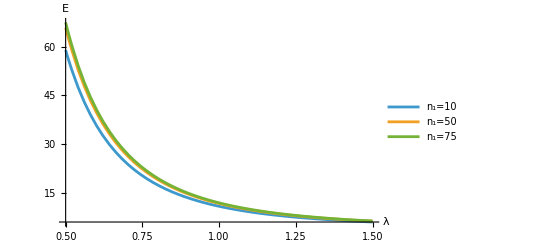

```mathematica
Plot[{E4Uni2[[3]]/.{kT->1,Subscript[n, a]->10,Subscript[n, b]->190},{E4Uni2[[3]]/.{kT->1,Subscript[n, a]->50,Subscript[n, b]->150}},{E4Uni2[[3]]/.{kT->1,Subscript[n, a]->75,Subscript[n, b]->125}}},{λ,0.5,1.5},PlotLegends->{"n_1=10","n_1=50","n_1=75"},AxesLabel->{λ,Ε}]
```

```mathematica
Export["EUni2_Gauss_Approx.csv",Table[{λv,E4Uni2[[If[λv<=1,3,1]]]/.{kT->1,Subscript[n, a]->100,Subscript[n, b]->100,λ->λv},E4Uni2[[If[λv<=1,3,1]]]/.{kT->1,Subscript[n, a]->50,Subscript[n, b]->150,λ->λv},E4Uni2[[If[λv<=1,3,1]]]/.{kT->1,Subscript[n, a]->25,Subscript[n, b]->175,λ->λv},E4Uni2[[If[λv<=1,3,1]]]/.{kT->1,Subscript[n, a]->10,Subscript[n, b]->190,λ->λv}},{λv,0.5,1.35,0.0125}]
]
```

EUni2_Gauss_Approx.csv

```mathematica
test13Solns
```

{{w_2→2-(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→-1+(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→-(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→-(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))},{w_2→-2+(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→1-(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→-(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→-(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))},{w_2→-2+(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→-1+(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))},{w_2→2-(3 (λ_1^2+λ_2^2))/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),w_3→1-(3 λ_1^2)/(λ_1^2+λ_2^2+λ_1^4 λ_2^4),yc_1→(√3 b (√n-√n_a) √(n n_a) λ_1 λ_2^2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_2→-(√3 b (√n-√n_a) √(n n_a) λ_1^2 λ_2)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4)),yc_3→-(√3 b (√n-√n_a) √(n n_a) λ_1^3 λ_2^3)/((n+3 n_a) (λ_1^2+λ_2^2+λ_1^4 λ_2^4))}}

```mathematica
ns={Subscript[n, a],n,n,n}
WKG11=Sum[WLang[(((√(1/(ns[[i]]^2*b^2)(FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}).(FUni.Qp.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]})))/.{b->1,Subscript[ω, 1]->0,Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]->Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3]})/.test13Solns[[1]])/.{Subscript[n, 1]->ns[[1]],Subscript[n, 2]->ns[[2]],Subscript[n, 3]->ns[[3]],Subscript[n, 4]->ns[[4]],n->ns[[2]],b->1,Subscript[λ, 1]->λa,Subscript[λ, 2]->λb},ns[[i]]],{i,1,4}];
```

{n_a,n,n,n}

```mathematica
N[WKG11/.{λa->1.1,λb->1/√1.1,Subscript[n, a]->70,n->110}]
```

6.05428

```mathematica
test22Solns
```

{{w_2→0,w_3→0,yc_1→(b n_a √n_b λ_1-b √n_a n_b λ_1)/(√3 (n_a+n_b)),yc_2→0,yc_3→0},{w_2→0,w_3→0,yc_1→(-b n_a √n_b λ_1+b √n_a n_b λ_1)/(√3 (n_a+n_b)),yc_2→0,yc_3→0},{w_1→0,w_3→0,yc_1→0,yc_2→(b n_a √n_b λ_2-b √n_a n_b λ_2)/(√3 (n_a+n_b)),yc_3→0},{w_1→0,w_3→0,yc_1→0,yc_2→(-b n_a √n_b λ_2+b √n_a n_b λ_2)/(√3 (n_a+n_b)),yc_3→0},{w_1→0,w_2→0,yc_1→0,yc_2→0,yc_3→(b n_a √n_b-b √n_a n_b)/(√3 (n_a+n_b) λ_1 λ_2)},{w_1→0,w_2→0,yc_1→0,yc_2→0,yc_3→(-b n_a √n_b+b √n_a n_b)/(√3 (n_a+n_b) λ_1 λ_2)}}

```mathematica
ns={Subscript[n, a],Subscript[n, a],Subscript[n, b],Subscript[n, b]}
WKG22s=Table[Sum[WLang[(√(1/(ns[[i]]^2*b^2)(FUni.Q4.cp4Rs[[i]]-{Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}).(FUni.Q4.cp4Rs[[i]]-{Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}))/.test22Solns[[k]])/.{Subscript[n, 1]->ns[[1]],Subscript[n, 2]->ns[[2]],Subscript[n, 3]->ns[[3]],Subscript[n, 4]->ns[[4]],Subscript[λ, 1]->λa,Subscript[λ, 2]->λb},ns[[i]]],{i,1,4}],
{k,{1,3,5}}];
```

{n_a,n_a,n_b,n_b}

```mathematica
N[WKG22s[[1]]/.{λa->1.1,λb->1/√1.1,Subscript[n, a]->80,Subscript[n, b]->120}]
```

6.10034

```mathematica
Length[cases2]
```

9

```mathematica
cases2
```

{{40,120,120,120},{70,110,110,110},{100,100,100,100},{130,90,90,90},{190,70,70,70},{250,50,50,50},{25,25,175,175},{50,50,150,150},{75,75,125,125}}

```mathematica
Export["WUni_KG_Approx.csv",Table[Catenate[{ {λ}, Table[If[i==3,
P4Chain[FUnif[λ],WLang,cases2[[i]]][[1]],
If[i<=6,
WKG11/.{Subscript[n, a]->cases2[[i,1]],n->cases2[[i,2]],λa->λ,λb->1/√λ},
WKG22s[[If[λ>=1,1,2]]]/.{Subscript[n, a]->cases2[[i,1]],Subscript[n, b]->cases2[[i,3]],λa->λ,λb->1/√λ}
]
],
{i,1,Length[cases2]}] }],{λ,0.5,3.75,0.05}]]
```

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. 2 √30 ComplexInfinity)/(√3) encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression (0. 2 √30 ComplexInfinity)/(√3) encountered.

Power::infy: Infinite expression 1/(√0.) encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression (0. 2 √30 ComplexInfinity)/(√3) encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

WUni_KG_Approx.csv

```mathematica
(*Export["WUni_KG_Approx.csv",Table[Catenate[{ {λ}, Table[If[i==3,
P4Chain[FUnif[λ],WLang,cases2[[i]]][[1]],
If[i<=6,
WKG11/.{Subscript[n, 1]->cases2[[i,1]],Subscript[n, 2]->cases2[[i,2]],Subscript[n, 3]->cases2[[i,3]],Subscript[n, 4]->cases2[[i,4]],n->cases2[[i,4]],λa->λ,λb->1/√λ},
WKG22/.{Subscript[n, 1]->cases2[[i,1]],Subscript[n, 2]->cases2[[i,2]],Subscript[n, 3]->cases2[[i,3]],Subscript[n, 4]->cases2[[i,4]],n->cases2[[i,4]],λa->λ,λb->1/√λ}
]
],
{i,{2,4,5,8,9}}] }],{λ,0.5,2.0,0.05}]]*)
```

```mathematica
cases2[[8]]
```

{50,50,150,150}

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {-17.1211,5.44679,8.21976,279.273,1603.96,1231.57}.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {-17.1212,5.4468,8.21977,279.273,1603.96,1231.57}.

FindMinimum::cvmit: Failed to converge to the requested accuracy or precision within 500 iterations.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {4.96536,3.49319,1.50336,22.5468,44.4839,1.86297}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::infeas: Possible infeasibility detected. Returning the best solution found. Setting a different initial point or Method -> InteriorPoint may lead to a better solution.

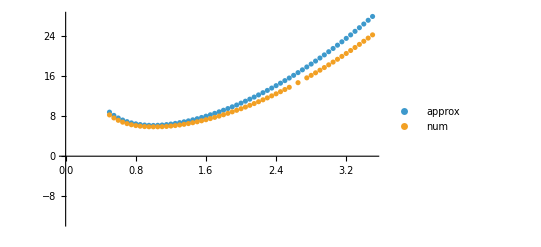

```mathematica
Block[{case},
case=cases2[[8]];
ListPlot[{
Table[{λ,WKG22s[[If[λ>=1,1,2]]]/.{Subscript[n, a]->cases2[[8,1]],Subscript[n, b]->cases2[[8,3]],λa->λ,λb->1/√λ}},{λ,0.5,3.5,0.05}],
Table[{λ,P4ChainLocal[FUnif[λ],WLang,case][[1]]},{λ,0.5,3.5,0.05}]
},PlotLegends->{"approx","num"},PlotRange->Automatic
]
]
```

```mathematica
WKG11sub=WKG11/.{λa->λ,λb->1/√λ};
WKG22subs=WKG22s/.{λa->λ,λb->1/√λ};
```

```mathematica
ΣKG1=D[WKG11sub,λ];
ΣKG2=D[WKG22subs,λ];
```

```mathematica
r0=b*√n;
l0=n*b;
γStar=Simplify[r0/l0*√((λ^2+(1/√λ)^2+(1/√λ)^2)/3),λ>0]
W8chain=Sum[WLang[γStar,n],{i,1,4}]
```

1/(√3 √((n λ)/(2+λ^3)))

4 n (Log[Csch[(√3)/(√((n λ)/(2+λ^3)))+1/(3 √3 ((n λ)/(2+λ^3))^(3/2) (1-1/(√3 √((n λ)/(2+λ^3)))))+((2+λ^3) Sin[7/(2 √3 √((n λ)/(2+λ^3)))])/(15 n λ)] ((√3)/(√((n λ)/(2+λ^3)))+1/(3 √3 ((n λ)/(2+λ^3))^(3/2) (1-1/(√3 √((n λ)/(2+λ^3)))))+((2+λ^3) Sin[7/(2 √3 √((n λ)/(2+λ^3)))])/(15 n λ))]+((√3)/(√((n λ)/(2+λ^3)))+1/(3 √3 ((n λ)/(2+λ^3))^(3/2) (1-1/(√3 √((n λ)/(2+λ^3)))))+((2+λ^3) Sin[7/(2 √3 √((n λ)/(2+λ^3)))])/(15 n λ))/(√3 √((n λ)/(2+λ^3))))

```mathematica
Σ8Chain=Simplify[D[W8chain,λ]];
```

```mathematica
(4!)/(2!*2!)
```

6

```mathematica
4!
```

24

```mathematica
p
```

p

```mathematica
Clear[p]
```

```mathematica
ΣKG4=p^4*(Σ8Chain/.{n->na,b->1})+p^3*(1-p)*(4!)/(3!*1!)(ΣKG1/.{Subscript[n, a]->na,n->nb,b->1})+p^2*(1-p)^2*(4!)/(2!*2!)(((ΣKG2[[If[λ>=1,1,2]]])/.{Subscript[n, a]->na,Subscript[n, b]->nb})/.{b->1})+p^1*(1-p)^3*(4!)/(1!*3!)(ΣKG1/.{Subscript[n, a]->nb,n->na,b->1})+(1-p)^4*(Σ8Chain/.{n->nb,b->1});
N[ΣKG4/.{p->0.5,na->100,nb->100,λ->1.001}]
```

Part::pkspec1: The expression If[λ≥1,1,2] cannot be used as a part specification.

General::stop: Further output of Part::pkspec1 will be suppressed during this calculation.

0.0120606

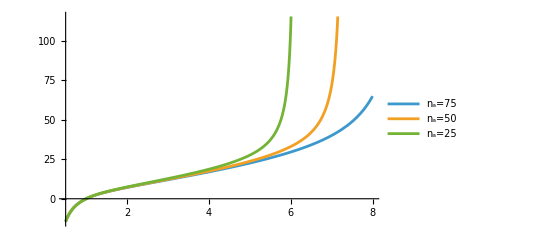

```mathematica
Plot[{ΣKG4/.{p->0.5,na->75,nb->75},ΣKG4/.{p->0.5,na->50,nb->100},ΣKG4/.{p->0.5,na->35,nb->115}},{λ,0.5,8},PlotLegends->{"n_a=75","n_a=50","n_a=25"}]
```

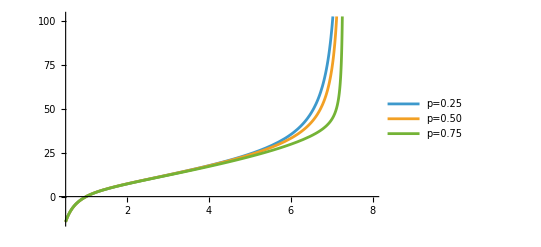

```mathematica
Plot[{ΣKG4/.{p->0.25,na->50,nb->100},ΣKG4/.{p->0.5,na->50,nb->100},ΣKG4/.{p->0.75,na->50,nb->100}},{λ,0.5,8},PlotLegends->{"p=0.25","p=0.50","p=0.75"}]
```

```mathematica
Quiet[Export["Sigma_KG_Approx_nanb.csv",Table[N[{λv,ΣKG4/.{p->0.5,na->75,nb->75,λ->λv},ΣKG4/.{p->0.5,na->50,nb->100,λ->λv},ΣKG4/.{p->0.5,na->25,nb->125,λ->λv}}],{λv,0.5,8,0.025}]]]
Quiet[Export["Sigma_KG_Approx_p.csv",Table[N[{λv,ΣKG4/.{p->0.1,na->50,nb->100,λ->λv},ΣKG4/.{p->0.25,na->50,nb->100,λ->λv},ΣKG4/.{p->0.5,na->50,nb->100,λ->λv},ΣKG4/.{p->0.75,na->50,nb->100,λ->λv},ΣKG4/.{p->0.9,na->50,nb->100,λ->λv}}],{λv,0.5,8,0.025}]]]
```

Sigma_KG_Approx_nanb.csv

Sigma_KG_Approx_p.csv

### 6-chain

```mathematica
c6Rs
```

{{r0,0,0},{0,r0,0},{0,0,r0},{-r0,0,0},{0,-r0,0},{0,0,-r0}}

```mathematica
cp6Rs={{b √Subscript[n, 1],0,0},{0,b √Subscript[n, 2],0},{0,0,b √Subscript[n, 3]},{-b √Subscript[n, 4],0,0},{0,-b √Subscript[n, 5],0},{0,0,-b √Subscript[n, 6]}}
```

{{b √n_1,0,0},{0,b √n_2,0},{0,0,b √n_3},{-b √n_4,0,0},{0,-b √n_5,0},{0,0,-b √n_6}}

```mathematica
P6ChainHat[F_,ω_,xc_,f_:WLang,nsv_:{100,100,100,100,100,100},bv_:1]:=Module[{Rs},
Rs=cp6Rs/.{Subscript[n, 1]->nsv[[1]],Subscript[n, 2]->nsv[[2]],Subscript[n, 3]->nsv[[3]],Subscript[n, 4]->nsv[[4]],Subscript[n, 5]->nsv[[5]],Subscript[n, 6]->nsv[[6]],b->1};
Sum[Block[{r,λ,R},
R=Rs[[i]];
r=N[F.(QRod[ω]).R-(QRod[ω]).xc];
λ=(√(r.r))/(nsv[[i]]*bv);
N[f[λ,nsv[[i]]]]
],{i,1,6}]
]
```

```mathematica
P6Chain[F_,f_:WLang,nsv_:{100,100,100,100,100,100},bv_:1]:=Module[{nmax},
nmax=Max[nsv];
NMinimize[{P6ChainHat[F,{ωx,ωy,ωz},{xc1,xc2,xc3},f,nsv,bv],{ωx,ωy,ωz}∈Ball[{0,0,0},2*Pi]&&{xc1,xc2,xc3}∈Ball[{0,0,0},nmax*bv]},{ωx,ωy,ωz,xc1,xc2,xc3}]
]
```

```mathematica
P6Chain[FUnif[1.1],WLang,{50,50,50,150,150,150}]
```

{8.87096,{ωx→1.15819,ωy→0.516793,ωz→-3.681,xc1→0.828359,xc2→0.828362,xc3→0.828359}}

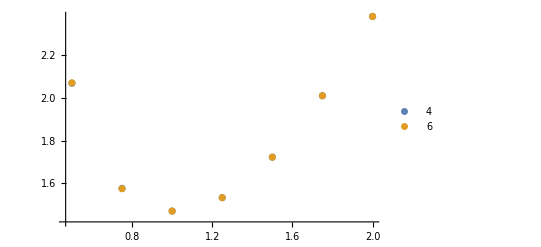

```mathematica
Block[{na,nb,λa,λb,dλ},
na=50;nb=150;
λa=0.5;
λb=2.0;
dλ=0.25;
ListPlot[{
Table[{λ,P4Chain[FUnif[λ],WLang,{na,na,nb,nb}][[1]]/4},{λ,λa,λb,dλ}],
Table[{λ,P6Chain[FUnif[λ],WLang,{na,na,na,nb,nb,nb}][[1]]/6},{λ,λa,λb,dλ}]
},PlotLegends->{"4","6"},PlotRange->Automatic
]
]
```

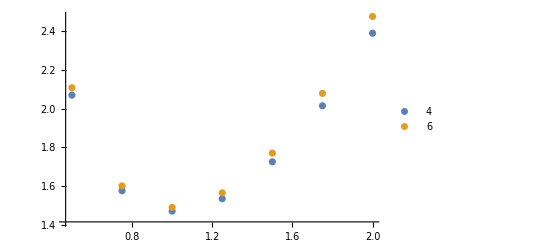

```mathematica
Block[{na,nb,λa,λb,dλ},
na=50;nb=150;
λa=0.5;
λb=2.0;
dλ=0.25;
ListPlot[{
Table[{λ,P4Chain[FUnif[λ],WLang,{40,120,120,120}][[1]]/4},{λ,λa,λb,dλ}],
Table[{λ,P6Chain[FUnif[λ],WLang,{40,112,112,112,112,112}][[1]]/6},{λ,λa,λb,dλ}]
},PlotLegends->{"4","6"},PlotRange->Automatic
]
]
```

```mathematica
Block[{na,nb,λa,λb,dλ},
na=50;nb=150;
λa=0.5;
λb=2.0;
dλ=0.25;
Export["WUni_4-vs-6.csv",Table[N[{λ,P4Chain[FUnif[λ],WLang,{na,na,nb,nb}][[1]]/4,P6Chain[FUnif[λ],WLang,{na,na,na,nb,nb,nb}][[1]]/6,P4Chain[FUnif[λ],WLang,{40,120,120,120}][[1]]/4,P6Chain[FUnif[λ],WLang,{40,112,112,112,112,112}][[1]]/6}],{λ,λa,λb,dλ}]]
]
```

WUni_4-vs-6.csv

## w/o Free Rotation

```mathematica
$Assumptions=θ∈Reals&&ϕ∈Reals&&ψ∈Reals
```

θ∈ℝ&&ϕ∈ℝ&&ψ∈ℝ

```mathematica
Qe=Simplify[Q[{0,0,1},ψ].Q[{0,1,0},θ].Q[{0,0,1},ϕ]]
```

{{Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ],-Cos[θ] Cos[ψ] Sin[ϕ]-Cos[ϕ] Sin[ψ],Cos[ψ] Sin[θ]},{Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ],Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ],Sin[θ] Sin[ψ]},{-Cos[ϕ] Sin[θ],Sin[θ] Sin[ϕ],Cos[θ]}}

```mathematica
FUni
```

{{λ_1,0,0},{0,λ_2,0},{0,0,1/(λ_1 λ_2)}}

```mathematica
W4NFRUni=Sum[3/2 kT *((FUni.Qe.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}).(FUni.Qe.cp4Rs[[i]]-{Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}))/(Subscript[n, i]*b^2),{i,1,4}];
```

```mathematica
ze={Subscript[xc, 1],Subscript[xc, 2],Subscript[xc, 3]}
```

{xc_1,xc_2,xc_3}

```mathematica
W4NFRUniGrad=Table[D[W4NFRUni,ze[[i]]],{i,1,3}]/.{Subscript[xc, 1]->ϵ*Subscript[yc, 1],Subscript[xc, 2]->ϵ*Subscript[yc, 2],Subscript[xc, 3]->ϵ*Subscript[yc, 3]};
```

```mathematica
zep={Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}
```

{yc_1,yc_2,yc_3}

```mathematica
W4NFRUniGradϵExpand=Simplify[Normal[Series[W4NFRUniGrad,{ϵ,0,1}]]]/.{ϵ->1}
```

{1/b^2 kT ((3 yc_1)/n_1+(3 yc_1)/n_2+(3 yc_1)/n_3-(3 b Cos[ψ] Sin[θ] λ_1)/(√n_1)+(b (Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) λ_1)/(√n_2)-(b (-Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (Cos[ϕ]-√3 Sin[ϕ]) Sin[ψ]) λ_1)/(√n_3)+(3 yc_1+b (Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])-√2 (Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) √n_4 λ_1)/n_4),1/b^2 kT ((3 yc_2)/n_1+(3 yc_2)/n_2+(3 yc_2)/n_3-(3 b Sin[θ] Sin[ψ] λ_2)/(√n_1)+(b (-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) λ_2)/(√n_2)+(b (-√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]-√3 Cos[θ] Sin[ψ])) λ_2)/(√n_3)+(3 yc_2+b (√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]+√3 Cos[θ] Sin[ψ])) √n_4 λ_2)/n_4),1/(b^2 n_1 n_2 n_3 n_4 λ_1 λ_2)kT (b (Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) n_1 n_2 n_3 √n_4+b (Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) n_1 n_2 √n_3 n_4+b (Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) n_1 √n_2 n_3 n_4-3 b Cos[θ] √n_1 n_2 n_3 n_4+3 (n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4))) yc_3 λ_1 λ_2)}

```mathematica
W4NFRUniLinSoln=Solve[W4NFRUniGradϵExpand=={0,0,0},zep]
```

{{yc_1→1/((3 kT)/(b^2 n_1)+(3 kT)/(b^2 n_2)+(3 kT)/(b^2 n_3)+(3 kT)/(b^2 n_4))((3 kT Cos[ψ] Sin[θ] λ_1)/(b √n_1)-(kT (Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) λ_1)/(b √n_2)+(kT (-Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (Cos[ϕ]-√3 Sin[ϕ]) Sin[ψ]) λ_1)/(b √n_3)-(kT (Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])-√2 (Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) λ_1)/(b √n_4)),yc_2→1/((3 kT)/(b^2 n_1)+(3 kT)/(b^2 n_2)+(3 kT)/(b^2 n_3)+(3 kT)/(b^2 n_4))((3 kT Sin[θ] Sin[ψ] λ_2)/(b √n_1)-(kT (-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) λ_2)/(b √n_2)-(kT (-√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]-√3 Cos[θ] Sin[ψ])) λ_2)/(b √n_3)-(kT (√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]+√3 Cos[θ] Sin[ψ])) λ_2)/(b √n_4)),yc_3→-1/(3 (n_1 n_2 n_3+n_1 n_2 n_4+n_1 n_3 n_4+n_2 n_3 n_4) λ_1 λ_2)b √n_1 √n_2 √n_3 (Cos[θ] √n_1 √n_2 √n_3-√6 Cos[ϕ] Sin[θ] √n_1 √n_2 √n_3+√2 Sin[θ] Sin[ϕ] √n_1 √n_2 √n_3+Cos[θ] √n_1 √n_2 √n_4+√6 Cos[ϕ] Sin[θ] √n_1 √n_2 √n_4+√2 Sin[θ] Sin[ϕ] √n_1 √n_2 √n_4+Cos[θ] √n_1 √n_3 √n_4-2 √2 Sin[θ] Sin[ϕ] √n_1 √n_3 √n_4-3 Cos[θ] √n_2 √n_3 √n_4) √n_4}}

```mathematica
figs2=Table[Block[{c4Rs,xs4ChainAll,xs4ChainPoly,F,QStar,xcStar,star},
xs4ChainAll=Import["four-chain.csv"];
xs4ChainPoly=Table[xs4ChainAll[[i]],{i,1,345}];
c4Rs={13.6*{0,0,1},37*{0,2*Sqrt[2]/3,-1/3},37*{Sqrt[2/3],-Sqrt[2]/3,-1/3},37*{-Sqrt[2/3],-Sqrt[2]/3,-1/3}};
F=FUnif[1.5];
QStar=N[Qe/.{ϕ->0,θ->α,ψ->0}];
star=P4NFRChainHatHat[F,{0,α,0},WLang,{50,100,100,100}];
xcStar={xc1,xc2,xc3}/.star[[2]];

Graphics3D[{
(*{
(*EdgeForm[Thick],*)
(*LightPink,*)
Opacity[0.0625],Dashed,Tetrahedron[c4Rs]
},*)
{
(*EdgeForm[Thick],*)
(*LightPink,*)
Opacity[0.125],Tetrahedron[Table[F.QStar.r+xcStar,{r,c4Rs}]]
},
{Yellow,Opacity[0.8],Cone[{F.QStar.({0,0,5}+c4Rs[[1]])+xcStar,F.QStar.c4Rs[[1]]+xcStar},1]},
{Table[Sphere[F.QStar.xs4ChainPoly[[i]]+xcStar,0.5],{i,1,Length[xs4ChainPoly]}]},
{Green,Sphere[xcStar,1.0]},
{Red,Sphere[{0,0,0},1.0]},
{Opacity[0.65],Table[Arrow[{xcStar,F.QStar.c4Rs[[i]]+xcStar}],{i,1,4}]}
},
Boxed->False
]
],{α,0,π/2,π/6}]
```

```mathematica
$Assumptions=$Assumptions&&Subscript[w, 1]∈Reals&&Subscript[w, 2]∈Reals&&Subscript[w, 3]∈Reals&&Subscript[yc, 1]∈Reals&&Subscript[yc, 2]∈Reals&&Subscript[yc, 3]∈Reals&&α∈Reals&&β∈Reals&&ξ&&Subscript[xc, 1]∈Reals&&Subscript[xc, 2]∈Reals&&Subscript[xc, 3]∈Reals&&λ∈Reals&&λ>=0&&γ∈Reals&&γ>=0
```

θ∈ℝ&&ϕ∈ℝ&&ψ∈ℝ&&w_1∈ℝ&&w_2∈ℝ&&w_3∈ℝ&&yc_1∈ℝ&&yc_2∈ℝ&&yc_3∈ℝ&&α∈ℝ&&β∈ℝ&&ξ&&xc_1∈ℝ&&xc_2∈ℝ&&xc_3∈ℝ&&λ∈ℝ&&λ≥0&&γ∈ℝ&&γ≥0

```mathematica
W4NFRUniLinSolnSimple=FullSimplify[W4NFRUniLinSoln]
```

{{yc_1→1/(3 n_2 n_3 n_4+3 n_1 (n_3 n_4+n_2 (n_3+n_4)))b (-n_1 √n_2 n_3 ((Cos[ψ] Sin[θ]+√2 (Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])-(Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ])) √n_2+(Cos[ψ] Sin[θ]+2 √2 (Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ])) √n_4) √n_4 λ_1+(-Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (Cos[ϕ]-√3 Sin[ϕ]) Sin[ψ]) n_1 n_2 √n_3 n_4 λ_1+3 Cos[ψ] Sin[θ] √n_1 n_2 n_3 n_4 λ_1),yc_2→1/(3 n_2 n_3 n_4+3 n_1 (n_3 n_4+n_2 (n_3+n_4)))(-b n_1 √n_2 n_3 ((√2 Cos[ψ] (Cos[ϕ]+√3 Sin[ϕ])+(√6 Cos[θ] Cos[ϕ]+Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_2+(-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_4) √n_4 λ_2+b (√2 Cos[ψ] (-Cos[ϕ]+√3 Sin[ϕ])-Sin[θ] Sin[ψ]+√2 Cos[θ] (√3 Cos[ϕ]+Sin[ϕ]) Sin[ψ]) n_1 n_2 √n_3 n_4 λ_2+3 b Sin[θ] Sin[ψ] √n_1 n_2 n_3 n_4 λ_2),yc_3→(3 b Cos[θ] √n_1 n_2 n_3 n_4-n_1 (b (Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) √n_2 n_3 n_4+n_2 (b (Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) n_3 √n_4+b (Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) √n_3 n_4)))/(3 (n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4))) λ_1 λ_2)}}

```mathematica
W4NFRUni=Simplify[(W4NFRUni/.{Subscript[xc, 1]->Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3]})/.W4NFRUniLinSolnSimple[[1]]]
```

1/(6 b^2)kT (1/(n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))^2 b^2 n_2 ((3 Cos[ψ] Sin[θ] √n_1 n_3 n_4+(Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) √n_2 n_3 n_4+n_1 ((-Cos[ψ] Sin[θ]-√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])+√2 (Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_3 √n_4+(-Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (Cos[ϕ]-√3 Sin[ϕ]) Sin[ψ]) √n_3 n_4+(Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) √n_2 (n_3+n_4)))^2 λ_1^2+1/(λ_1^2 λ_2^2)(3 Cos[θ] √n_1 n_3 n_4+(Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) √n_2 n_3 n_4+n_1 (-((Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) n_3 √n_4)-(Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) √n_3 n_4+(Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) √n_2 (n_3+n_4)))^2+(3 Sin[θ] Sin[ψ] √n_1 n_3 n_4+(-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_2 n_3 n_4+n_1 (-((√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]+√3 Cos[θ] Sin[ψ])) n_3 √n_4)+(√6 Cos[ψ] Sin[ϕ]+(-Sin[θ]+√2 Cos[θ] Sin[ϕ]) Sin[ψ]+Cos[ϕ] (-√2 Cos[ψ]+√6 Cos[θ] Sin[ψ])) √n_3 n_4-(2 √2 Cos[ϕ] Cos[ψ]-(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_2 (n_3+n_4)))^2 λ_2^2)+1/(n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))^2 b^2 n_1 (((Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])-√2 (Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_2 n_3 √n_4+(Cos[ψ] Sin[θ]-√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (-Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_2 √n_3 n_4+(Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) √n_2 n_3 n_4+3 Cos[ψ] Sin[θ] √n_1 (n_3 n_4+n_2 (n_3+n_4)))^2 λ_1^2+1/(λ_1^2 λ_2^2)((Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) n_2 n_3 √n_4+(Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) n_2 √n_3 n_4+(Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) √n_2 n_3 n_4+3 Cos[θ] √n_1 (n_3 n_4+n_2 (n_3+n_4)))^2+((√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]+√3 Cos[θ] Sin[ψ])) n_2 n_3 √n_4+(-√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]-√3 Cos[θ] Sin[ψ])) n_2 √n_3 n_4+(-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_2 n_3 n_4+3 Sin[θ] Sin[ψ] √n_1 (n_3 n_4+n_2 (n_3+n_4)))^2 λ_2^2)+1/n_3(b^2 (-Cos[ψ] Sin[θ] √n_3 λ_1+√2 (Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ]) √n_3 λ_1+√6 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) √n_3 λ_1+1/(n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))(-3 Cos[ψ] Sin[θ] √n_1 n_2 n_3 n_4 λ_1+n_1 ((Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])-√2 (Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_2 n_3 √n_4 λ_1+(Cos[ψ] Sin[θ]-√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (-Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_2 √n_3 n_4 λ_1+(Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) √n_2 n_3 n_4 λ_1)))^2+1/((n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))^2 λ_1^2 λ_2^2)b^2 n_3^2 (3 Cos[θ] √n_1 n_2 n_4+(Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) n_2 √n_3 n_4+n_1 (n_2 ((Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) √n_3-(Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) √n_4)-(Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) √n_2 n_4+(Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) √n_3 n_4))^2+(b Sin[θ] Sin[ψ] √n_3 λ_2-√6 b (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) √n_3 λ_2+√2 b (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) √n_3 λ_2+1/(n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))(3 b Sin[θ] Sin[ψ] √n_1 n_2 n_3 n_4 λ_2-n_1 (b (√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]+√3 Cos[θ] Sin[ψ])) n_2 n_3 √n_4 λ_2+b (-√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]-√3 Cos[θ] Sin[ψ])) n_2 √n_3 n_4 λ_2+b (-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_2 n_3 n_4 λ_2)))^2)+1/n_4(b^2 (Cos[ψ] Sin[θ] √n_4 λ_1-√2 (Cos[θ] Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[ψ]) √n_4 λ_1+√6 (Cos[θ] Cos[ϕ] Cos[ψ]-Sin[ϕ] Sin[ψ]) √n_4 λ_1-1/(n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))(-3 Cos[ψ] Sin[θ] √n_1 n_2 n_3 n_4 λ_1+n_1 ((Cos[ψ] Sin[θ]+√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]-Sin[ϕ])-√2 (Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_2 n_3 √n_4 λ_1+(Cos[ψ] Sin[θ]-√2 Cos[θ] Cos[ψ] (√3 Cos[ϕ]+Sin[ϕ])+√2 (-Cos[ϕ]+√3 Sin[ϕ]) Sin[ψ]) n_2 √n_3 n_4 λ_1+(Cos[ψ] (Sin[θ]+2 √2 Cos[θ] Sin[ϕ])+2 √2 Cos[ϕ] Sin[ψ]) √n_2 n_3 n_4 λ_1)))^2+1/((n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))^2 λ_1^2 λ_2^2)b^2 (3 Cos[θ] √n_1 n_2 n_3-n_1 ((Cos[θ]-2 √2 Sin[θ] Sin[ϕ]) √n_2 n_3+n_2 ((Cos[θ]+√2 Sin[θ] (√3 Cos[ϕ]+Sin[ϕ])) √n_3-(Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) √n_4)-(Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) n_3 √n_4)+(Cos[θ]+√2 Sin[θ] (-√3 Cos[ϕ]+Sin[ϕ])) n_2 n_3 √n_4)^2 n_4^2+(b Sin[θ] Sin[ψ] √n_4 λ_2+√6 b (Cos[ψ] Sin[ϕ]+Cos[θ] Cos[ϕ] Sin[ψ]) √n_4 λ_2+√2 b (Cos[ϕ] Cos[ψ]-Cos[θ] Sin[ϕ] Sin[ψ]) √n_4 λ_2+1/(n_2 n_3 n_4+n_1 (n_3 n_4+n_2 (n_3+n_4)))(3 b Sin[θ] Sin[ψ] √n_1 n_2 n_3 n_4 λ_2-n_1 (b (√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]+√3 Cos[θ] Sin[ψ])) n_2 n_3 √n_4 λ_2+b (-√6 Cos[ψ] Sin[ϕ]+(Sin[θ]-√2 Cos[θ] Sin[ϕ]) Sin[ψ]+√2 Cos[ϕ] (Cos[ψ]-√3 Cos[θ] Sin[ψ])) n_2 √n_3 n_4 λ_2+b (-2 √2 Cos[ϕ] Cos[ψ]+(Sin[θ]+2 √2 Cos[θ] Sin[ϕ]) Sin[ψ]) √n_2 n_3 n_4 λ_2)))^2))

```mathematica
figs2=Table[Block[{c4Rs,xs4ChainAll,xs4ChainPoly,F,QStar,xcStar,star,αSubs,xcSubs,λ},
λ=2.0;
xs4ChainAll=Import["four-chain.csv"];
xs4ChainPoly=Table[xs4ChainAll[[i]],{i,1,345}];
c4Rs={13.6*{0,0,1},37*{0,2*Sqrt[2]/3,-1/3},37*{Sqrt[2/3],-Sqrt[2]/3,-1/3},37*{-Sqrt[2/3],-Sqrt[2]/3,-1/3}};
F=FUnif[λ];
αSubs={ψ->0,ϕ->0,θ->θv};
xcStar=(({Subscript[yc, 1],Subscript[yc, 2],Subscript[yc, 3]}/.W4NFRUniLinSolnSimple[[1]])/.{Subscript[n, 1]->30,Subscript[n, 2]->100,Subscript[n, 3]->100,Subscript[n, 4]->100,b->1,kT->1,Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ})/.αSubs;
QStar=N[Qe/.αSubs];
Print[xcStar," ",QStar];
Export["Fixed-Frame-RVE-"<>ToString[Round[θv*100]]<>".pdf",Graphics3D[{
(*{
(*EdgeForm[Thick],*)
(*LightPink,*)
Opacity[0.0625],Dashed,Tetrahedron[c4Rs]
},*)
{
(*EdgeForm[Thick],*)
(*LightPink,*)
Opacity[0.125],Tetrahedron[Table[F.QStar.r+xcStar,{r,c4Rs}]]
},
{Yellow,Opacity[0.8],Cone[{F.QStar.({0,0,5}+c4Rs[[1]])+xcStar,F.QStar.c4Rs[[1]]+xcStar},1]},
{Table[Sphere[F.QStar.xs4ChainPoly[[i]]+xcStar,0.5],{i,1,Length[xs4ChainPoly]}]},
{Green,Sphere[xcStar,1.25]},
{Red,Sphere[{0,0,0},1.25]},
{Opacity[0.65],Table[Arrow[{xcStar,F.QStar.c4Rs[[i]]+xcStar}],{i,1,4}]}
},
Boxed->False
]
]],{θv,0,π/2,π/6}]
```

{0.,0.,0.921928} {{1.,0.,0.},{0.,1.,0.},{0.,0.,1.}}

{1.3038,0.,0.798413} {{0.866025,0.,0.5},{0.,1.,0.},{-0.5,0.,0.866025}}

{2.25825,0.,0.460964} {{0.5,0.,0.866025},{0.,1.,0.},{-0.866025,0.,0.5}}

{2.60761,0.,0.} {{0.,0.,1.},{0.,1.,0.},{-1.,0.,0.}}

{Fixed-Frame-RVE-0.pdf,Fixed-Frame-RVE-52.pdf,Fixed-Frame-RVE-105.pdf,Fixed-Frame-RVE-157.pdf}

```mathematica
figs2[[2]]
```

-Graphics3D-

```mathematica
W4NFRUni1=Simplify[W4NFRUni/.{Subscript[n, 2]->n,Subscript[n, 3]->n,Subscript[n, 4]->n}]
```

1/(16 (n+3 n_1) λ_1^2 λ_2^2)kT (n (20-12 Cos[2 θ]+(26+6 Cos[2 θ]+3 Cos[2 θ-2 ψ]-6 Cos[2 ψ]+3 Cos[2 (θ+ψ)]) λ_1^4 λ_2^2+(26+6 Cos[2 θ]-3 Cos[2 θ-2 ψ]+6 Cos[2 ψ]-3 Cos[2 (θ+ψ)]) λ_1^2 λ_2^4)+3 n_1 (-4 (-7+Cos[2 θ])+(30+2 Cos[2 θ]+Cos[2 θ-2 ψ]-2 Cos[2 ψ]+Cos[2 (θ+ψ)]) λ_1^4 λ_2^2-(-30-2 Cos[2 θ]+Cos[2 θ-2 ψ]-2 Cos[2 ψ]+Cos[2 (θ+ψ)]) λ_1^2 λ_2^4)+48 √n √n_1 (Cos[θ]^2+Cos[ψ]^2 Sin[θ]^2 λ_1^4 λ_2^2+Sin[θ]^2 Sin[ψ]^2 λ_1^2 λ_2^4))

```mathematica
W4NFRUni2=Simplify[W4NFRUni/.{Subscript[n, 2]->Subscript[n, 1],Subscript[n, 3]->n,Subscript[n, 4]->n}]
```

1/(3 (n+n_1) λ_1^2 λ_2^2)kT (n (5 Cos[θ]^2+(5+Cos[2 ϕ]) Sin[θ]^2-2 √2 Cos[θ] Sin[θ] Sin[ϕ]+(Cos[θ]^2 (5+Cos[2 ϕ]) Cos[ψ]^2+Cos[ψ]^2 (5 Sin[θ]^2+√2 Sin[2 θ] Sin[ϕ])-4 Cos[θ] Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]+4 Cos[ϕ]^2 Sin[ψ]^2+6 Sin[ϕ]^2 Sin[ψ]^2+√2 Cos[ϕ] Sin[θ] Sin[2 ψ]) λ_1^4 λ_2^2+(6 Cos[ψ]^2 Sin[ϕ]^2-2 √2 Cos[ϕ] Cos[ψ] Sin[θ] Sin[ψ]+5 Sin[θ]^2 Sin[ψ]^2+√2 Sin[2 θ] Sin[ϕ] Sin[ψ]^2+4 Cos[θ]^2 Sin[ϕ]^2 Sin[ψ]^2+Cos[ϕ]^2 (4 Cos[ψ]^2+6 Cos[θ]^2 Sin[ψ]^2)+Cos[θ] Sin[2 ϕ] Sin[2 ψ]) λ_1^2 λ_2^4)+n_1 (5 Cos[θ]^2+(5+Cos[2 ϕ]) Sin[θ]^2-2 √2 Cos[θ] Sin[θ] Sin[ϕ]+(Cos[θ]^2 (5+Cos[2 ϕ]) Cos[ψ]^2+Cos[ψ]^2 (5 Sin[θ]^2+√2 Sin[2 θ] Sin[ϕ])-4 Cos[θ] Cos[ϕ] Cos[ψ] Sin[ϕ] Sin[ψ]+4 Cos[ϕ]^2 Sin[ψ]^2+6 Sin[ϕ]^2 Sin[ψ]^2+√2 Cos[ϕ] Sin[θ] Sin[2 ψ]) λ_1^4 λ_2^2+(6 Cos[ψ]^2 Sin[ϕ]^2-2 √2 Cos[ϕ] Cos[ψ] Sin[θ] Sin[ψ]+5 Sin[θ]^2 Sin[ψ]^2+√2 Sin[2 θ] Sin[ϕ] Sin[ψ]^2+4 Cos[θ]^2 Sin[ϕ]^2 Sin[ψ]^2+Cos[ϕ]^2 (4 Cos[ψ]^2+6 Cos[θ]^2 Sin[ψ]^2)+Cos[θ] Sin[2 ϕ] Sin[2 ψ]) λ_1^2 λ_2^4)+2 √n √n_1 (Cos[θ]^2+Sin[ϕ] (√2 Sin[2 θ]+2 Sin[θ]^2 Sin[ϕ])+(Cos[ψ]^2 (Sin[θ]^2-2 √2 Cos[θ] Sin[θ] Sin[ϕ]+2 Cos[θ]^2 Sin[ϕ]^2)-2 √2 Cos[ϕ] Cos[ψ] Sin[θ] Sin[ψ]+2 Cos[ϕ]^2 Sin[ψ]^2+Cos[θ] Sin[2 ϕ] Sin[2 ψ]) λ_1^4 λ_2^2+(2 Cos[ϕ]^2 Cos[ψ]^2+(Sin[θ]^2-2 √2 Cos[θ] Sin[θ] Sin[ϕ]+2 Cos[θ]^2 Sin[ϕ]^2) Sin[ψ]^2+Cos[ϕ] (-4 Cos[θ] Cos[ψ] Sin[ϕ] Sin[ψ]+√2 Sin[θ] Sin[2 ψ])) λ_1^2 λ_2^4))

```mathematica
sa=Integrate[Sin[θ],{ϕ,0,2*π},{θ,0,π},{ψ,0,2*π}]
```

8 π^2

```mathematica
W4NFRUni1Avg=Simplify[Integrate[W4NFRUni1*Sin[θ],{ϕ,0,2*π},{θ,0,π},{ψ,0,2*π}]/sa]
```

(kT (3 n+2 √n √n_1+11 n_1) (1+λ_1^4 λ_2^2+λ_1^2 λ_2^4))/(2 (n+3 n_1) λ_1^2 λ_2^2)

```mathematica
W4NFRUni2Avg=Simplify[Integrate[W4NFRUni2*Sin[θ],{ϕ,0,2*π},{θ,0,π},{ψ,0,2*π}]/sa]
```

(kT (5 n+2 √n √n_1+5 n_1) (1+λ_1^4 λ_2^2+λ_1^2 λ_2^4))/(3 (n+n_1) λ_1^2 λ_2^2)

```mathematica
W4NFRs1=W4NFRUni1Avg/.{Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ}
W4NFRs2=W4NFRUni2Avg/.{Subscript[λ, 1]->λ,Subscript[λ, 2]->1/√λ}
```

(kT (2+λ^3) (3 n+2 √n √n_1+11 n_1))/(2 λ (n+3 n_1))

(kT (2+λ^3) (5 n+2 √n √n_1+5 n_1))/(3 λ (n+n_1))

```mathematica
Σ4NFR1=Simplify[D[W4NFRUni1Avg,Subscript[λ, 1]]]
Σ4NFR2=Simplify[D[W4NFRUni2Avg,Subscript[λ, 1]]]
Σ4NFRs1=Simplify[D[W4NFRs1,λ]]
Σ4NFRs2=Simplify[D[W4NFRs2,λ]]
E4NFRs1=Simplify[D[W4NFRs1,{λ,2}]]
E4NFRs2=Simplify[D[W4NFRs2,{λ,2}]]
```

(kT (3 n+2 √n √n_1+11 n_1) (-1+λ_1^4 λ_2^2))/((n+3 n_1) λ_1^3 λ_2^2)

(2 kT (5 n+2 √n √n_1+5 n_1) (-1+λ_1^4 λ_2^2))/(3 (n+n_1) λ_1^3 λ_2^2)

(kT (-1+λ^3) (3 n+2 √n √n_1+11 n_1))/(λ^2 (n+3 n_1))

(2 kT (-1+λ^3) (5 n+2 √n √n_1+5 n_1))/(3 λ^2 (n+n_1))

(kT (2+λ^3) (3 n+2 √n √n_1+11 n_1))/(λ^3 (n+3 n_1))

(2 kT (2+λ^3) (5 n+2 √n √n_1+5 n_1))/(3 λ^3 (n+n_1))

```mathematica
E4NFRs1/.{λ->1}
```

(3 kT (3 n+2 √n √n_1+11 n_1))/(n+3 n_1)

```mathematica
E4NFRs2/.{λ->1}
```

(2 kT (5 n+2 √n √n_1+5 n_1))/(n+n_1)

```mathematica
E4Uni
```

1/((1+2 λ^3)^5 (n+3 n_1))kT (-18 (1-10 λ^3-129 λ^6-40 λ^9+16 λ^12) Cos[(√2 (-1+λ^3))/(1+2 λ^3)] (√n-√n_1)^2-486 √2 λ^3 (-1+4 λ^6) Sin[(√2 (-1+λ^3))/(1+2 λ^3)] (√n-√n_1)^2+((1+2 λ^3)^2 (n (8+61 λ^3-6 λ^6+148 λ^9+32 λ^12)-18 √n λ^3 (1-14 λ^3+4 λ^6) √n_1+3 (8+55 λ^3+78 λ^6+124 λ^9+32 λ^12) n_1))/λ^3)

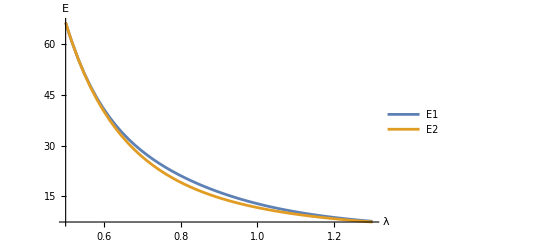

```mathematica
Plot[{E4Uni/.{kT->1,Subscript[n, 1]->250,n->50},E4NFRs1/.{kT->1,Subscript[n, 1]->250,n->50}
},{λ,0.5,1.3},PlotLegends->{"E1","E2"},AxesLabel->{λ,Ε}]
```

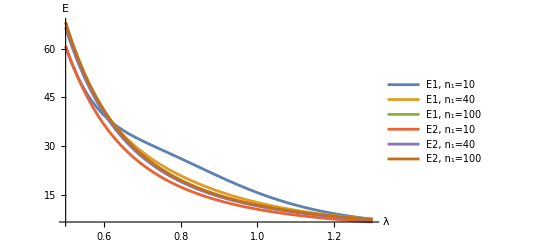

```mathematica
Plot[{E4Uni/.{kT->1,Subscript[n, 1]->10,n->130},E4Uni/.{kT->1,Subscript[n, 1]->40,n->120},E4Uni/.{kT->1,Subscript[n, 1]->100,n->100},
E4NFRs1/.{kT->1,Subscript[n, 1]->10,n->130},E4NFRs1/.{kT->1,Subscript[n, 1]->40,n->120},E4NFRs1/.{kT->1,Subscript[n, 1]->100,n->100}
},{λ,0.5,1.3},PlotLegends->{"E1, n_1=10","E1, n_1=40","E1, n_1=100","E2, n_1=10","E2, n_1=40","E2, n_1=100"},AxesLabel->{λ,Ε}]
```

```mathematica
(*
Export["EUni_Gauss_Approx.csv",Table[{λv,E4Uni/.{kT->1,Subscript[n, 1]->10,n->130,λ->λv},E4Uni/.{kT->1,Subscript[n, 1]->40,n->120,λ->λv},E4Uni/.{kT->1,Subscript[n, 1]->100,n->100,λ->λv},E4Uni/.{kT->1,Subscript[n, 1]->325,n->25,λ->λv}},{λv,0.5,1.35,0.0125}]]
Export["EUni2_Gauss_Approx.csv",Table[{λv,E4Uni2/.{kT->1,Subscript[n, 1]->100,n->100,λ->λv},E4Uni2/.{kT->1,Subscript[n, 1]->50,n->150,λ->λv},E4Uni2/.{kT->1,Subscript[n, 1]->25,n->175,λ->λv},E4Uni2/.{kT->1,Subscript[n, 1]->10,n->190,λ->λv}},{λv,0.5,1.35,0.0125}]
]*)
```

```mathematica
Export["EUni_Fixed.csv",Table[{λv,
E4NFRs1/.{kT->1,Subscript[n, 1]->10,n->130,λ->λv},E4NFRs1/.{kT->1,Subscript[n, 1]->40,n->120,λ->λv},E4NFRs1/.{kT->1,Subscript[n, 1]->100,n->100,λ->λv},E4NFRs1/.{kT->1,Subscript[n, 1]->250,n->50,λ->λv},
E4NFRs2/.{kT->1,Subscript[n, 1]->10,n->190,λ->λv},E4NFRs2/.{kT->1,Subscript[n, 1]->25,n->175,λ->λv},E4NFRs2/.{kT->1,Subscript[n, 1]->50,n->150,λ->λv}
},{λv,0.5,1.35,0.0125}]
]
```

EUni_Fixed.csv

```mathematica
Qe
```

{{Cos[θ] Cos[ϕ],-Sin[θ],Cos[θ] Sin[ϕ]},{Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ],Cos[θ] Cos[ψ],Cos[ψ] Sin[θ] Sin[ϕ]-Cos[ϕ] Sin[ψ]},{-Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ],Cos[θ] Sin[ψ],Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ]}}

```mathematica
P4NFRChainHat[F_,αs_,xc_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{Rs,QNFR},
Rs=cp4Rs/.{Subscript[n, 1]->nsv[[1]],Subscript[n, 2]->nsv[[2]],Subscript[n, 3]->nsv[[3]],Subscript[n, 4]->nsv[[4]],b->1};
QNFR=N[Qe/.{ϕ->αs[[1]],θ->αs[[2]],ψ->αs[[3]]}];
Sum[Block[{r,λ,R},
R=Rs[[i]];
r=N[F.(QNFR).R-QNFR.xc];
λ=(√(r.r))/(nsv[[i]]*bv);
N[f[λ,nsv[[i]]]]
],{i,1,4}]
]
```

```mathematica
P4NFRChainHat[FUnif[1.1],{0,π/4,0},{0,1,0},WGauss,{70,110,110,110},1]
```

1.52968

```mathematica
NMinimize[{P4NFRChainHat[FUnif[1.1],{0,π/4,0},{xc1,xc2,xc3},WGauss,{70,110,110,110},1],{xc1,xc2,xc3}∈Ball[{0,0,0},100]},{xc1,xc2,xc3}][[1]]
```

1.5093

```mathematica
P4NFRChainHatHat[F_,αs_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{nmax,QNFR},
nmax=Max[nsv];
NMinimize[{P4NFRChainHat[F,αs,{xc1,xc2,xc3},f,nsv,bv],{xc1,xc2,xc3}∈Ball[{0,0,0},nmax*bv]},{xc1,xc2,xc3}][[1]]
]
```

```mathematica
P4NFRChainHatHat[FUnif[1.1],{0,π/4,0},WGauss,{70,110,110,110},1]
```

1.50929

```mathematica
P4NFRChain[F_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{},
NIntegrate[P4NFRChainHatHat[F,{ϕ,θ,ψ},f,nsv,bv]*Sin[θ],{ϕ,0,2*π},{θ,0,π},{ψ,0,2*π}]/sa
]
(*P4NFRChainLocal[F_,f_:WLang,nsv_:{100,100,100,100},bv_:1]:=Module[{},
NIntegrate[FindMinimum[P4ChainHat[F,{ϕ,θ,ψ},{xc1,xc2,xc3},f,nsv,bv],{xc1,0},{xc2,0},{xc3,0}][[1]]*Sin[θ],{ϕ,0,2*π},{θ,0,π},{ψ,0,2*π}]
]*)
```

```mathematica
(*P4NFRChain[FUnif[1.1],WGauss]*)
```

NMinimize::nnum: The function value 1/4 (0.015 ((-39.78 Cos[«1»] Cos[«1»]+32.0657 Sin[«1»]-40.5949 Cos[«1»] Sin[«1»])^2+(-31.3749 Cos[«1»] Cos[«1»]-40.1065 Plus[«2»]-38.5835 Plus[«2»])^2+(-31.3749 Cos[«1»] Sin[«1»]-38.5835 Plus[«2»]-40.1065 Plus[«2»])^2)+0.015 ((«1»)^2+(«1»)^2+(«1»)^2)+0.015 ((«1»)^2+«1»+(«1»)^2)+0.015 ((-30.7985 Cos[«1»] Cos[«1»]+«19» Sin[«1»]-25.9282 Cos[«1»] Sin[«1»])^2+(-26.8802 Cos[«1»] Cos[«1»]-«1»-«1»)^2+(«1»)^2)) is not a number at {xc1,xc2,xc3} = {30.7985,26.8802,36.9282}.

NIntegrate::inumr: The integrand 1/4 Sin[θ] (0.015 ((-1. xc1 Cos[«1»] Cos[«1»]+9.42809 Plus[«2»]+1. xc2 Sin[«1»]-1. xc3 Cos[«1»] Sin[«1»]-3.33333 Plus[«2»])^2+(-1. xc2 Cos[«1»] Cos[«1»]+9.42809 Plus[«2»]-1. xc3 Plus[«2»]-1. xc1 Plus[«2»]-3.33333 Plus[«2»])^2+(-1. xc2 Cos[«1»] Sin[«1»]+9.42809 Plus[«2»]-1. xc1 Plus[«2»]-1. xc3 Plus[«2»]-3.33333 Plus[«2»])^2)+0.015 ((«1»)^2+(«1»)^2+(«1»)^2)+0.015 ((«1»)^2+(«1»)^2+(«1»)^2)+0.015 ((-1. xc1 Cos[«1»] Cos[«1»]+«3»+10. Plus[«2»])^2+(«1»)^2+(«1»)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

NIntegrate::inumr: The integrand ({xc1,xc2,xc3}∈Ball[{0,0,0},100]) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

NIntegrate::inumr: The integrand 1/4 Sin[θ] (0.015 ((-1. xc1 Cos[«1»] Cos[«1»]+9.42809 Plus[«2»]+1. xc2 Sin[«1»]-1. xc3 Cos[«1»] Sin[«1»]-3.33333 Plus[«2»])^2+(-1. xc2 Cos[«1»] Cos[«1»]+9.42809 Plus[«2»]-1. xc3 Plus[«2»]-1. xc1 Plus[«2»]-3.33333 Plus[«2»])^2+(-1. xc2 Cos[«1»] Sin[«1»]+9.42809 Plus[«2»]-1. xc1 Plus[«2»]-1. xc3 Plus[«2»]-3.33333 Plus[«2»])^2)+0.015 ((«1»)^2+(«1»)^2+(«1»)^2)+0.015 ((«1»)^2+(«1»)^2+(«1»)^2)+0.015 ((-1. xc1 Cos[«1»] Cos[«1»]+«3»+10. Plus[«2»])^2+(«1»)^2+(«1»)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

{1/(8 π^2)NIntegrate[1/4 Sin[θ] (0.015 ((-1. xc1 Cos[θ] Cos[ϕ]+9.42809 (0.-1.1 Sin[θ])+1. xc2 Sin[θ]-1. xc3 Cos[θ] Sin[ϕ]-3.33333 (0.+1.1 Cos[θ] Sin[ϕ]))^2+(-1. xc2 Cos[θ] Cos[ψ]+9.42809 (0.+0.953463 Cos[θ] Cos[ψ])-1. xc3 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ])-1. xc1 (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ])-3.33333 (0.+0.953463 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ])))^2+(-1. xc2 Cos[θ] Sin[ψ]+9.42809 (0.+0.953463 Cos[θ] Sin[ψ])-1. xc1 (-1. Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ])-1. xc3 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])-3.33333 (0.+0.953463 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])))^2)+0.015 ((-1. xc1 Cos[θ] Cos[ϕ]-8.16497 (0.+1.1 Cos[θ] Cos[ϕ])-4.71405 (0.-1.1 Sin[θ])+1. xc2 Sin[θ]-1. xc3 Cos[θ] Sin[ϕ]-3.33333 (0.+1.1 Cos[θ] Sin[ϕ]))^2+(-1. xc2 Cos[θ] Cos[ψ]-4.71405 (0.+0.953463 Cos[θ] Cos[ψ])-1. xc3 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ])-1. xc1 (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ])-3.33333 (0.+0.953463 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ]))-8.16497 (0.+0.953463 (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ])))^2+(-1. xc2 Cos[θ] Sin[ψ]-4.71405 (0.+0.953463 Cos[θ] Sin[ψ])-1. xc1 (-1. Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ])-1. xc3 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])-8.16497 (0.+0.953463 (-1. Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ]))-3.33333 (0.+0.953463 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])))^2)+0.015 ((-1. xc1 Cos[θ] Cos[ϕ]+8.16497 (0.+1.1 Cos[θ] Cos[ϕ])-4.71405 (0.-1.1 Sin[θ])+1. xc2 Sin[θ]-1. xc3 Cos[θ] Sin[ϕ]-3.33333 (0.+1.1 Cos[θ] Sin[ϕ]))^2+(-1. xc2 Cos[θ] Cos[ψ]-4.71405 (0.+0.953463 Cos[θ] Cos[ψ])-1. xc3 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ])-1. xc1 (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ])-3.33333 (0.+0.953463 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ]))+8.16497 (0.+0.953463 (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ])))^2+(-1. xc2 Cos[θ] Sin[ψ]-4.71405 (0.+0.953463 Cos[θ] Sin[ψ])-1. xc1 (-1. Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ])-1. xc3 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])+8.16497 (0.+0.953463 (-1. Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ]))-3.33333 (0.+0.953463 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])))^2)+0.015 ((-1. xc1 Cos[θ] Cos[ϕ]+1. xc2 Sin[θ]-1. xc3 Cos[θ] Sin[ϕ]+10. (0.+1.1 Cos[θ] Sin[ϕ]))^2+(-1. xc2 Cos[θ] Cos[ψ]-1. xc3 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ])-1. xc1 (Cos[ϕ] Cos[ψ] Sin[θ]+Sin[ϕ] Sin[ψ])+10. (0.+0.953463 (Cos[ψ] Sin[θ] Sin[ϕ]-1. Cos[ϕ] Sin[ψ])))^2+(-1. xc2 Cos[θ] Sin[ψ]-1. xc1 (-1. Cos[ψ] Sin[ϕ]+Cos[ϕ] Sin[θ] Sin[ψ])-1. xc3 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])+10. (0.+0.953463 (Cos[ϕ] Cos[ψ]+Sin[θ] Sin[ϕ] Sin[ψ])))^2)),{ϕ,0,2 π},{θ,0,π},{ψ,0,2 π}],NIntegrate[({xc1,xc2,xc3}∈Ball[{0,0,0},100]) Sin[θ],{ϕ,0,2 π},{θ,0,π},{ψ,0,2 π}]/(8 π^2)}

```mathematica
(*P4NFRUniNum1=Block[{nAvg,n1,n2},
nAvg=100;
n1=(4*nAvg)/10;
n2=(4*nAvg-n1)/3;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4NFRChain[FUnif[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.5,2.0,0.1}]
]*)
```

100, 40, 120

NMinimize::nnum: The function value 1/4 (0.0125 ((-41.3693 Cos[«1»] Cos[«1»]+34.785 Sin[«1»]-46.0665 Cos[«1»] Sin[«1»])^2+(-39.506 Cos[«1»] Cos[«1»]-49.4047 Plus[«2»]-49.5463 Plus[«2»])^2+(-39.506 Cos[«1»] Sin[«1»]-49.5463 Plus[«2»]-49.4047 Plus[«2»])^2)+0.0125 ((«1»+«1»-«1»)^2+((«1»«1»)^2+(«1»)^2)+«7» «1»+0.0375 ((-36.8972 Cos[«1»] Cos[«1»]+«18» Sin[«1»]-41.0785 Cos[«1»] Sin[«1»])^2+(«1»)^2+(-32.203 Cos[«1»] Sin[«1»]-«1»-«1»)^2)) is not a number at {xc1,xc2,xc3} = {36.8972,32.203,44.2408}.

NIntegrate::inumr: The integrand 1/4 «1» (0.0125 ((-1. xc1 Cos[«1»] Cos[«1»]+10.328 Plus[«2»]+1. xc2 Sin[«1»]-1. xc3 Cos[«1»] Sin[«1»]-3.65148 Plus[«2»])^2+(-1. xc2 Cos[«1»] Cos[«1»]+10.328 Plus[«2»]-«1»-1. xc1 Plus[«2»]-3.65148 Plus[«2»])^2+(-1. xc2 Cos[«1»] Sin[«1»]+10.328 Plus[«2»]-1. xc1 Plus[«2»]-1. xc3 Plus[«2»]-3.65148 Plus[«2»])^2)+0.0125 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0125 ((«1»)^2+«1»+«1»)+0.0375 ((-1. xc1 Cos[«1»] Cos[«1»]+«3»+6.32456 Plus[«1»])^2+(«1»)^2+(«1»)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

NIntegrate::inumr: The integrand ({xc1,xc2,xc3}∈Ball[{0,0,0},120]) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

NIntegrate::inumr: The integrand 1/4 «1» (0.0125 ((-1. xc1 Cos[«1»] Cos[«1»]+10.328 Plus[«2»]+1. xc2 Sin[«1»]-1. xc3 Cos[«1»] Sin[«1»]-3.65148 Plus[«2»])^2+(-1. xc2 Cos[«1»] Cos[«1»]+10.328 Plus[«2»]-«1»-1. xc1 Plus[«2»]-3.65148 Plus[«2»])^2+(-1. xc2 Cos[«1»] Sin[«1»]+10.328 Plus[«2»]-1. xc1 Plus[«2»]-1. xc3 Plus[«2»]-3.65148 Plus[«2»])^2)+0.0125 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0125 ((«1»)^2+«1»+«1»)+0.0375 ((-1. xc1 Cos[«1»] Cos[«1»]+«3»+6.32456 Plus[«1»])^2+(«1»)^2+(«1»)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::nnum: The function value 1/4 (0.0125 ((-42.2638 Cos[«1»] Cos[«1»]+35.3014 Sin[«1»]-46.4317 Cos[«1»] Sin[«1»])^2+(-38.8697 Cos[«1»] Cos[«1»]-48.9548 Plus[«2»]-48.4442 Plus[«2»])^2+(-38.8697 Cos[«1»] Sin[«1»]-48.4442 Plus[«2»]-48.9548 Plus[«2»])^2)+0.0125 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0125 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0375 ((-36.8972 Cos[«1»] Cos[«1»]+«18» Sin[«1»]-40.446 Cos[«1»] Sin[«1»])^2+(«1»)^2+(«1»)^2)) is not a number at {xc1,xc2,xc3} = {36.8972,32.203,44.2408}.

NMinimize::nnum: The function value 1/4 (0.0125 ((-43.1582 Cos[«1»] Cos[«1»]+35.8178 Sin[«1»]-46.7968 Cos[«1»] Sin[«1»])^2+(-38.3752 Cos[«1»] Cos[«1»]-48.6051 Plus[«2»]-47.5877 Plus[«2»])^2+(-38.3752 Cos[«1»] Sin[«1»]-47.5877 Plus[«2»]-48.6051 Plus[«2»])^2)+0.0125 ((«1»+«1»-«1»)^2+(«1»)^2+(«1»)^2)+«7» «1»+0.0375 ((-36.8972 Cos[«1»] Cos[«1»]+«18» Sin[«1»]-39.8136 Cos[«1»] Sin[«1»])^2+(«1»)^2+(-32.203 Cos[«1»] Sin[«1»]-«1»-«1»)^2)) is not a number at {xc1,xc2,xc3} = {36.8972,32.203,44.2408}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

```mathematica
(*P4NFRUniNum2=Block[{nAvg,n1,n2},
nAvg=100;
n1=70;
n2=(4*nAvg-n1)/3;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4NFRChain[FUnif[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.5,2.0,0.1}]
]*)
```

100, 70, 110

NMinimize::nnum: The function value 1/4 (0.0136364 ((-38.1296 Cos[«1»] Cos[«1»]+32.0137 Sin[«1»]-42.3325 Cos[«1»] Sin[«1»])^2+(-36.5337 Cos[«1»] Cos[«1»]-45.5286 Plus[«2»]-45.9585 Plus[«2»])^2+(-36.5337 Cos[«1»] Sin[«1»]-45.9585 Plus[«2»]-45.5286 Plus[«2»])^2)+0.0136364 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0136364 («1»)+0.0214286 ((-33.8479 Cos[«1»] Cos[«1»]+«1»-36.4012 Cos[«1»] Sin[«1»])^2+(«1»)^2+(«1»)^2)) is not a number at {xc1,xc2,xc3} = {33.8479,29.5416,40.5845}.

NIntegrate::inumr: The integrand 1/4 «1» (0.0136364 ((-1. xc1 Cos[«1»] Cos[«1»]+9.88826 Plus[«2»]+1. xc2 Sin[«1»]-1. xc3 Cos[«1»] Sin[«1»]-3.49603 Plus[«2»])^2+(-1. xc2 Cos[«1»] Cos[«1»]+9.88826 Plus[«2»]-1. xc3 «1»-1. xc1 Plus[«2»]-3.49603 Plus[«2»])^2+(-1. xc2 Cos[«1»] Sin[«1»]+9.88826 Plus[«2»]-1. xc1 Plus[«2»]-1. xc3 Plus[«2»]-3.49603 Plus[«2»])^2)+0.0136364 («1»)+«1»+0.0214286 ((-1. xc1 Cos[«1»] Cos[«1»]+«3»+«18» Plus[«1»])^2+(«5»+«18» «1»)^2+(«1»)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

NIntegrate::inumr: The integrand ({xc1,xc2,xc3}∈Ball[{0,0,0},110]) Sin[θ] has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

NIntegrate::inumr: The integrand 1/4 «1» (0.0136364 ((-1. xc1 Cos[«1»] Cos[«1»]+9.88826 Plus[«2»]+1. xc2 Sin[«1»]-1. xc3 Cos[«1»] Sin[«1»]-3.49603 Plus[«2»])^2+(-1. xc2 Cos[«1»] Cos[«1»]+9.88826 Plus[«2»]-1. xc3 «1»-1. xc1 Plus[«2»]-3.49603 Plus[«2»])^2+(-1. xc2 Cos[«1»] Sin[«1»]+9.88826 Plus[«2»]-1. xc1 Plus[«2»]-1. xc3 Plus[«2»]-3.49603 Plus[«2»])^2)+0.0136364 («1»)+«1»+0.0214286 ((-1. xc1 Cos[«1»] Cos[«1»]+«3»+«18» Plus[«1»])^2+(«5»+«18» «1»)^2+(«1»)^2)) has evaluated to non-numerical values for all sampling points in the region with boundaries {{0,6.28319},{0,3.14159},{0,6.28319}}.

General::stop: Further output of NIntegrate::inumr will be suppressed during this calculation.

NMinimize::nnum: The function value 1/4 (0.0136364 ((-38.9859 Cos[«1»] Cos[«1»]+32.5081 Sin[«1»]-42.6821 Cos[«1»] Sin[«1»])^2+(-35.9245 Cos[«1»] Cos[«1»]-45.0979 Plus[«2»]-44.9033 Plus[«2»])^2+(-35.9245 Cos[«1»] Sin[«1»]-44.9033 Plus[«2»]-45.0979 Plus[«2»])^2)+0.0136364 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0136364 («1»)+0.0214286 ((-33.8479 Cos[«1»] Cos[«1»]+«1»-35.5645 «1» Sin[«1»])^2+(«1»)^2+(«1»)^2)) is not a number at {xc1,xc2,xc3} = {33.8479,29.5416,40.5845}.

NMinimize::nnum: The function value 1/4 (0.0136364 ((-39.8423 Cos[«1»] Cos[«1»]+33.0025 Sin[«1»]-43.0317 Cos[«1»] Sin[«1»])^2+(-35.451 Cos[«1»] Cos[«1»]-44.7631 Plus[«2»]-44.0832 Plus[«2»])^2+(-35.451 Cos[«1»] Sin[«1»]-44.0832 Plus[«2»]-44.7631 Plus[«2»])^2)+0.0136364 ((«1»)^2+(«1»)^2+(«1»)^2)+0.0136364 («1»)+0.0214286 ((-33.8479 Cos[«1»] Cos[«1»]+«1»-34.7279 Cos[«1»] Sin[«1»])^2+(«1»)^2+(«1»)^2)) is not a number at {xc1,xc2,xc3} = {33.8479,29.5416,40.5845}.

General::stop: Further output of NMinimize::nnum will be suppressed during this calculation.

```mathematica
(*shearSubs1={Subscript[ω, 1]->0,Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]->Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3],Subscript[n, 2]->n,Subscript[n, 3]->n,Subscript[n, 4]->n}/.W4ShearLinSoln1[[1]];*)
```

Part::partd: Part specification W4ShearLinSoln1⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*W4Shear1=Simplify[W4Shear/.shearSubs1]*)
```

```mathematica
(*W4Shear1=W4Shear/.shearSubs1;*)
```

ReplaceAll::reps: {{ω_1→0,ω_2→w_2,ω_3→w_3,xc_1→yc_1,xc_2→yc_2,xc_3→yc_3,n_2→n,n_3→n,n_4→n}/.W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*N[W4Shear1/.{kT->1,Subscript[n, 1]->40,n->130,s->1,b->1}]*)
```

ReplaceAll::reps: {W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{ω_1→0,ω_2→w_2,ω_3→w_3,xc_1→yc_1,xc_2→yc_2,xc_3→yc_3,130_2→130,130_3→130,130_4→130}/.W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

W4Shear/.({ω_1→0.,ω_2→w_2,ω_3→w_3,xc_1→yc_1,xc_2→yc_2,xc_3→yc_3,130._2→130.,130._3→130.,130._4→130.}/.W4ShearLinSoln1⟦1⟧)

```mathematica
(*shearSubs2={Subscript[ω, 1]->0,Subscript[ω, 2]->Subscript[w, 2],Subscript[ω, 3]->Subscript[w, 3],Subscript[xc, 1]->Subscript[yc, 1],Subscript[xc, 2]->Subscript[yc, 2],Subscript[xc, 3]->Subscript[yc, 3],Subscript[n, 2]->Subscript[n, 1],Subscript[n, 3]->n,Subscript[n, 4]->n}/.W4ShearLinSoln2[[1]];*)
```

Part::partd: Part specification W4ShearLinSoln2⟦1⟧ is longer than depth of object.

ReplaceAll::reps: {W4ShearLinSoln2⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*W4Shear2=W4Shear/.shearSubs2;*)
```

ReplaceAll::reps: {{ω_1→0,ω_2→w_2,ω_3→w_3,xc_1→yc_1,xc_2→yc_2,xc_3→yc_3,n_2→n_1,n_3→n,n_4→n}/.W4ShearLinSoln2⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

```mathematica
(*Show[{ListPlot[{Table[{P4ShearTestNum1[[i,1]],P4ShearTestNum1[[i,2,1]]},{i,1,Length[P4ShearTestNum1]}],Table[{P4ShearTestNum2[[i,1]],P4ShearTestNum2[[i,2,1]]},{i,1,Length[P4ShearTestNum2]}]}],Plot[{W4Shear1/.{kT->1,Subscript[n, 1]->40,n->130,b->1},W4Shear1/.{kT->1,Subscript[n, 1]->70,n->110,b->1}},{s,0,1.2}]}]*)
```

ReplaceAll::reps: {W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {{ω_1→0,ω_2→w_2,ω_3→w_3,xc_1→yc_1,xc_2→yc_2,xc_3→yc_3,130_2→130,130_3→130,130_4→130}/.W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {W4ShearLinSoln1⟦1⟧} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

-Graphics-

## Simple Shear

```mathematica
$Assumptions=θ∈Reals&&ϕ∈Reals&&ψ∈Reals
```

θ∈ℝ&&ϕ∈ℝ&&ψ∈ℝ

```mathematica
shearF[s_]:={{1,0,s},{0,1,0},{0,0,1}};
FShear=shearF[s];
CShear=Simplify[Transpose[FShear].FShear]
EigenSystemShear=Simplify[Eigensystem[CShear],s∈Reals]
λ3=√(EigenSystemShear[[1]][[2]]);
λ2=√(EigenSystemShear[[1]][[1]]);
λ1=√(EigenSystemShear[[1]][[3]]);
ϕ1=Simplify[Normalize[EigenSystemShear[[2]][[3]]],s∈Reals]
ϕ2=EigenSystemShear[[2]][[1]]
ϕ3=Simplify[Normalize[EigenSystemShear[[2]][[2]]],s∈Reals]
QShear=Transpose[{ϕ1,ϕ2,ϕ3}]
```

{{1,0,s},{0,1,0},{s,0,1+s^2}}

{{1,1/2 (2+s^2-s √(4+s^2)),1/2 (2+s^2+s √(4+s^2))},{{0,1,0},{1/2 (-s-√(4+s^2)),0,1},{1/2 (-s+√(4+s^2)),0,1}}}

{(-s+√(4+s^2))/(√(4+(s-√(4+s^2))^2)),0,2/(√(4+(s-√(4+s^2))^2))}

{0,1,0}

{(-s-√(4+s^2))/(√(4+(s+√(4+s^2))^2)),0,2/(√(4+(s+√(4+s^2))^2))}

{{(-s+√(4+s^2))/(√(4+(s-√(4+s^2))^2)),0,(-s-√(4+s^2))/(√(4+(s+√(4+s^2))^2))},{0,1,0},{2/(√(4+(s-√(4+s^2))^2)),0,2/(√(4+(s+√(4+s^2))^2))}}

```mathematica
Simplify[λ1]
```

(√(2+s^2+s √(4+s^2)))/(√2)

```mathematica
λ1
```

(√(2+s^2+s √(4+s^2)))/(√2)

```mathematica
λ2
```

1

```mathematica
λ3
```

(√(2+s^2-s √(4+s^2)))/(√2)

```mathematica
Simplify[λ1*λ2*λ3]
```

1/2 √(2+s^2-s √(4+s^2)) √(2+s^2+s √(4+s^2))

```mathematica
(*W4Shear=Simplify[()/.{Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2}]*)
```

```mathematica
P4ShearTestNum1=Block[{nAvg,n1,n2},
nAvg=100;
n1=(4*nAvg)/10;
n2=(4*nAvg-n1)/3;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[shearF[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.0,1.2,0.1}]
]
```

100, 40, 120

{{0.,{5.86603,{ωx→0.431355,ωy→-3.83189,ωz→-3.406,xc1→2.43445×10^-8,xc2→-5.85678×10^-8,xc3→1.33654}}},{0.1,{5.87194,{ωx→-0.935753,ωy→-4.81539,ωz→-2.34139,xc1→0.0650575,xc2→-0.0262768,xc3→1.40328}}},{0.2,{5.91642,{ωx→-0.278867,ωy→-5.48641,ωz→-0.723701,xc1→0.146195,xc2→-0.0148997,xc3→1.46953}}},{0.3,{5.99935,{ωx→-0.17052,ωy→-5.5481,ωz→-0.459332,xc1→0.229785,xc2→-0.0141388,xc3→1.5348}}},{0.4,{6.12066,{ωx→-0.0342918,ωy→-5.59545,ωz→-0.0959146,xc1→0.319706,xc2→-0.00391862,xc3→1.59865}}},{0.5,{6.33253,{ωx→6.04002,ωy→0.573402,ωz→1.63334,xc1→0.668264,xc2→0.0000111408,xc3→1.33653}}},{0.6,{6.47799,{ωx→-0.336652,ωy→-5.52973,ωz→-1.01645,xc1→0.512364,xc2→-0.0626186,xc3→1.72059}}},{0.7,{6.71384,{ωx→-0.383077,ωy→-5.50857,ωz→-1.20197,xc1→0.616331,xc2→-0.0861384,xc3→1.77806}}},{0.8,{6.98772,{ωx→-0.294321,ωy→-5.58966,ωz→-0.959706,xc1→0.729111,xc2→-0.0769955,xc3→1.83291}}},{0.9,{7.29954,{ωx→-0.298321,ωy→-5.60142,ωz→-1.01079,xc1→0.843453,xc2→-0.0900957,xc3→1.885}}},{1.,{7.64925,{ωx→-0.258216,ωy→-5.64375,ωz→-0.90895,xc1→0.963086,xc2→-0.0883113,xc3→1.93425}}},{1.1,{8.03678,{ωx→-0.310578,ωy→-5.61612,ωz→-1.13548,xc1→1.08271,xc2→-0.120117,xc3→1.98064}}},{1.2,{8.46208,{ωx→-0.309522,ωy→-5.62699,ωz→-1.17486,xc1→1.20718,xc2→-0.133204,xc3→2.02418}}}}

```mathematica
P4ShearTestNum2=Block[{nAvg,n1,n2},
nAvg=100;
n1=70;
n2=(4*nAvg-n1)/3;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[shearF[λ],WGauss,{n1,n2,n2,n2}]},{λ,0.0,1.2,0.1}]
]
```

100, 70, 110

{{0.,{5.9789,{ωx→2.13956,ωy→-0.546343,ωz→-4.06208,xc1→-1.25773×10^-7,xc2→-2.63359×10^-7,xc3→0.58175}}},{0.1,{5.99669,{ωx→-0.0211279,ωy→-5.52243,ωz→-0.053243,xc1→0.0305387,xc2→-0.000235896,xc3→0.610801}}},{0.2,{6.05424,{ωx→-1.39263,ωy→-0.622615,ωz→-3.6143,xc1→-0.0426532,xc2→-0.047667,xc3→0.639635}}},{0.3,{6.15155,{ωx→-1.37892,ωy→-0.705889,ωz→-3.71427,xc1→-0.0585912,xc2→-0.0812922,xc3→0.668046}}},{0.4,{6.28861,{ωx→-1.36779,ωy→-0.810635,ωz→-3.82587,xc1→-0.0668163,xc2→-0.122079,xc3→0.69584}}},{0.5,{6.46539,{ωx→-0.468299,ωy→0.546684,ωz→-1.36074,xc1→0.0277463,xc2→0.178569,xc3→0.722845}}},{0.6,{6.68189,{ωx→-0.109442,ωy→-5.63162,ωz→-0.330512,xc1→0.224504,xc2→-0.00873137,xc3→0.748914}}},{0.7,{6.93809,{ωx→-0.0848904,ωy→0.613113,ωz→-0.266356,xc1→0.260685,xc2→0.0735983,xc3→0.773931}}},{0.8,{7.23397,{ωx→0.687523,ωy→-2.46623,ωz→-0.210849,xc1→0.273098,xc2→0.165096,xc3→0.797806}}},{0.9,{7.56954,{ωx→0.639282,ωy→-5.19034,ωz→2.16607,xc1→0.358181,xc2→0.0895914,xc3→0.820479}}},{1.,{7.94477,{ωx→1.74089,ωy→3.14005,ωz→-0.49455,xc1→0.223017,xc2→-0.357028,xc3→0.841916}}},{1.1,{8.35965,{ωx→1.72877,ωy→3.13104,ωz→-0.472849,xc1→0.2526,xc2→-0.401272,xc3→0.862105}}},{1.2,{8.81419,{ωx→1.71707,ωy→3.12223,ωz→-0.452358,xc1→0.283123,xc2→-0.446425,xc3→0.881056}}}}

```mathematica
(*W13sub*)
```

```mathematica
WHookean=2 kT (Subscript[λ, 1]^2+1/(Subscript[λ, 1]^2 Subscript[λ, 2]^2)+Subscript[λ, 2]^2)
```

2 kT (λ_1^2+1/(λ_1^2 λ_2^2)+λ_2^2)

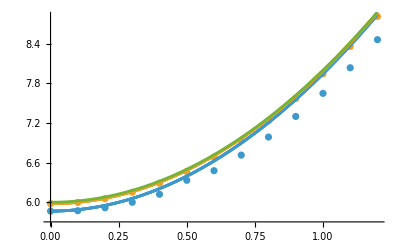

```mathematica
Show[{ListPlot[{Table[{P4ShearTestNum1[[i,1]],P4ShearTestNum1[[i,2,1]]},{i,1,Length[P4ShearTestNum1]}],Table[{P4ShearTestNum2[[i,1]],P4ShearTestNum2[[i,2,1]]},{i,1,Length[P4ShearTestNum2]}]}],Plot[{W13s/.{b->1,kT->1,Subscript[n, a]->40,n->120,Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2},W13s/.{b->1,kT->1,Subscript[n, a]->70,n->110,Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2},WHookean/.{kT->1,Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2}},{s,0,1.2}]}]
```

```mathematica
P4ShearTestNum3=Block[{nAvg,n1,n2},
nAvg=100;
n1=50;
n2=(4*nAvg-2*n1)/2;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[shearF[λ],WGauss,{n1,n1,n2,n2}]},{λ,0.0,2.0,0.1}]
]
```

100, 50, 150

{{0.,{5.86603,{ωx→4.98519,ωy→-2.44936,ωz→-0.791542,xc1→3.23751×10^-9,xc2→1.05662,xc3→0.747146}}},{0.1,{5.88558,{ωx→3.62885,ωy→-1.22232,ωz→-4.98154,xc1→0.0745881,xc2→1.05664,xc3→0.74713}}},{0.2,{5.91642,{ωx→-0.0783642,ωy→3.36791,ωz→-2.04527,xc1→0.133641,xc2→1.13356,xc3→0.861368}}},{0.3,{5.99935,{ωx→-0.105063,ωy→3.35552,ωz→-2.00077,xc1→0.211531,xc2→1.17277,xc3→0.915384}}},{0.4,{6.12066,{ωx→-0.129634,ωy→3.34156,ωz→-1.95913,xc1→0.296424,xc2→1.2123,xc3→0.96657}}},{0.5,{6.28023,{ωx→1.0766,ωy→0.856663,ωz→0.175048,xc1→0.344367,xc2→1.19316,xc3→1.09768}}},{0.6,{6.56995,{ωx→3.31023,ωy→-3.97445,ωz→-3.56715,xc1→0.448299,xc2→1.05664,xc3→0.747135}}},{0.7,{6.82414,{ωx→3.31027,ωy→-3.97443,ωz→-3.56713,xc1→0.523019,xc2→1.05664,xc3→0.74713}}},{0.8,{6.98772,{ωx→-4.09464,ωy→-2.04821,ωz→2.48575,xc1→0.685898,xc2→1.55468,xc3→0.875233}}},{0.9,{7.29954,{ωx→-4.0634,ωy→-1.82947,ωz→2.7155,xc1→0.779643,xc2→1.63935,xc3→0.842853}}},{1.,{7.64925,{ωx→-4.13308,ωy→-1.76984,ωz→2.66308,xc1→0.89101,xc2→1.69547,xc3→0.846084}}},{1.1,{8.03678,{ωx→-4.37735,ωy→-2.03113,ωz→2.00919,xc1→1.03952,xc2→1.66897,xc3→0.961347}}},{1.2,{8.68172,{ωx→4.94347,ωy→-3.55151,ωz→-1.558,xc1→0.896616,xc2→1.05669,xc3→0.747067}}},{1.3,{9.17055,{ωx→3.37279,ωy→-4.60104,ωz→-2.63309,xc1→0.971316,xc2→1.05664,xc3→0.747123}}},{1.4,{9.6985,{ωx→2.99143,ωy→-4.60954,ωz→-3.04662,xc1→1.04604,xc2→1.0566,xc3→0.747151}}},{1.5,{10.2655,{ωx→2.99145,ωy→-4.60952,ωz→-3.04663,xc1→1.12076,xc2→1.05664,xc3→0.747114}}},{1.6,{10.8717,{ωx→2.99146,ωy→-4.60952,ωz→-3.04662,xc1→1.19548,xc2→1.05667,xc3→0.747089}}},{1.7,{11.517,{ωx→2.99147,ωy→-4.60951,ωz→-3.04662,xc1→1.27021,xc2→1.05669,xc3→0.747066}}},{1.8,{12.2013,{ωx→6.24131,ωy→-0.172359,ωz→-0.70335,xc1→1.34489,xc2→1.05664,xc3→0.747156}}},{1.9,{12.9248,{ωx→6.24132,ωy→-0.172342,ωz→-0.703304,xc1→1.41964,xc2→1.05663,xc3→0.747149}}},{2.,{13.6874,{ωx→6.02884,ωy→-0.2139,ωz→-1.75663,xc1→1.49465,xc2→1.05656,xc3→0.747057}}}}

```mathematica
P4ShearTestNum4=Block[{nAvg,n1,n2},
nAvg=100;
n1=80;
n2=(4*nAvg-2*n1)/2;
Print[nAvg,", ",n1,", ",n2];
Table[{λ,P4Chain[shearF[λ],WGauss,{n1,n1,n2,n2}]},{λ,0.0,2.0,0.1}]
]
```

100, 80, 120

{{0.,{5.9798,{ωx→-1.90163,ωy→-5.70072,ωz→-0.411904,xc1→1.1308×10^-7,xc2→0.464231,xc3→0.328261}}},{0.1,{5.99767,{ωx→-3.76215,ωy→-3.16596,ωz→0.0541774,xc1→0.02759,xc2→0.480838,xc3→0.353952}}},{0.2,{6.05533,{ωx→-3.81185,ωy→-3.13128,ωz→0.00664003,xc1→0.0577778,xc2→0.496643,xc3→0.380412}}},{0.3,{6.15276,{ωx→-3.86208,ωy→-3.09475,ωz→-0.0367766,xc1→0.0905608,xc2→0.511569,xc3→0.407398}}},{0.4,{6.28994,{ωx→-3.91022,ωy→-3.05685,ωz→-0.0860914,xc1→0.12575,xc2→0.525348,xc3→0.43496}}},{0.5,{6.46686,{ωx→-3.96107,ωy→-3.01679,ωz→-0.120945,xc1→0.163546,xc2→0.538328,xc3→0.462316}}},{0.6,{6.6835,{ωx→-4.00537,ωy→-2.97674,ωz→-0.175922,xc1→0.203168,xc2→0.549533,xc3→0.490601}}},{0.7,{6.93986,{ωx→-4.05782,ωy→-2.93308,ωz→-0.196571,xc1→0.245716,xc2→0.560702,xc3→0.517154}}},{0.8,{7.23592,{ωx→-4.10097,ωy→-2.89083,ωz→-0.244226,xc1→0.289466,xc2→0.569598,xc3→0.544988}}},{0.9,{7.59434,{ωx→2.64601,ωy→-2.2683,ωz→-5.22799,xc1→0.295402,xc2→0.464229,xc3→0.328261}}},{1.,{7.97306,{ωx→2.64502,ωy→-2.264,ωz→-5.23035,xc1→0.328262,xc2→0.464239,xc3→0.328257}}},{1.1,{8.39165,{ωx→2.64503,ωy→-2.264,ωz→-5.23035,xc1→0.361089,xc2→0.46424,xc3→0.328256}}},{1.2,{8.81697,{ωx→-2.27928,ωy→-2.32487,ωz→-2.64726,xc1→-0.0314089,xc2→0.405337,xc3→0.918215}}},{1.3,{9.3114,{ωx→-2.29602,ωy→-2.32811,ωz→-2.67189,xc1→-0.0231716,xc2→0.387849,xc3→0.972975}}},{1.4,{9.84547,{ωx→0.887635,ωy→-2.54981,ωz→1.14181,xc1→0.562444,xc2→0.889427,xc3→0.291678}}},{1.5,{10.4192,{ωx→0.873693,ωy→-2.56142,ωz→1.15552,xc1→0.614612,xc2→0.913801,xc3→0.283342}}},{1.6,{11.0325,{ωx→0.859998,ωy→-2.57244,ωz→1.16853,xc1→0.667623,xc2→0.937167,xc3→0.274618}}},{1.7,{11.6855,{ωx→0.846572,ωy→-2.58288,ωz→1.18086,xc1→0.721371,xc2→0.959551,xc3→0.265565}}},{1.8,{12.3781,{ωx→0.833503,ωy→-2.59278,ωz→1.19254,xc1→0.775738,xc2→0.981009,xc3→0.256211}}},{1.9,{13.1104,{ωx→0.820817,ωy→-2.60216,ωz→1.20358,xc1→0.830633,xc2→1.00159,xc3→0.246589}}},{2.,{13.8822,{ωx→0.808587,ωy→-2.61107,ωz→1.214,xc1→0.885958,xc2→1.02136,xc3→0.236707}}}}

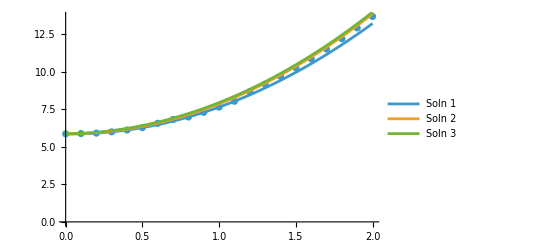
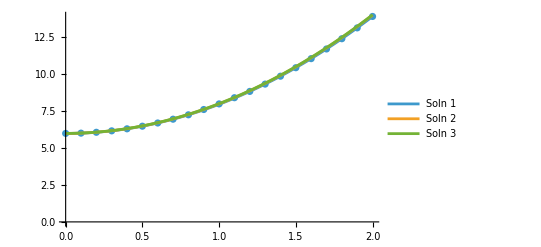

```mathematica
Block[{expr1,expr2},
expr1=Table[(W22s[[k]]/.{kT->1,Subscript[n, a]->50,Subscript[n, b]->150,Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2})/.{b->1},{k,{1,3,5}}];
expr2=Table[(W22s[[k]]/.{kT->1,Subscript[n, a]->80,Subscript[n, b]->120,Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2})/.{b->1},{k,{1,3,5}}];
{Show[{ListPlot[Table[{P4ShearTestNum3[[i,1]],P4ShearTestNum3[[i,2,1]]},{i,1,Length[P4ShearTestNum3]}](*,Table[{P4ShearTestNum4[[i,1]],P4ShearTestNum4[[i,2,1]]},{i,1,Length[P4ShearTestNum4]}]*)],Plot[(*Join[expr1,expr2]*)expr1,{s,0.0,2.0},PlotRange->{5,Automatic},PlotLegends->{"Soln 1","Soln 2","Soln 3"}]}],
Show[{ListPlot[Table[{P4ShearTestNum4[[i,1]],P4ShearTestNum4[[i,2,1]]},{i,1,Length[P4ShearTestNum4]}](*,Table[{P4ShearTestNum4[[i,1]],P4ShearTestNum4[[i,2,1]]},{i,1,Length[P4ShearTestNum4]}]*)],Plot[(*Join[expr1,expr2]*)expr2,{s,0.0,2.0},PlotRange->{5,Automatic},PlotLegends->{"Soln 1","Soln 2","Soln 3"}]}]}
]
```

```mathematica
(*expr1=Table[W22s[[k]]/.{kT->1,Subscript[n, a]->50,Subscript[n, b]->150,Subscript[λ, 1]->λ1,Subscript[λ, 2]->λ2},{k,{1,3,5}}];*)
```

```mathematica
Export["WShear_Gauss_Num.csv",Table[Catenate[{ {s}, Table[P4ChainLocal[shearF[s],WGauss,case][[1]],{case,cases}] }],{s,0.0,2.0,0.05}]]
```

WShear_Gauss_Num.csv

```mathematica
idx=1;
Do[
Print[case];
Export["WShear_Gauss_NumSoln_case-"<>ToString[idx]<>".csv",Table[Catenate[{ {s}, 
Block[{caseSoln,Qcase,xp},
caseSoln=P4ChainLocal[shearF[s],WGauss,case];
Qcase=QRod[{ωx,ωy,ωz}/.caseSoln[[2]]];
xp=(Transpose[Qcase].{xc1,xc2,xc3})/.caseSoln[[2]];
{caseSoln[[1]],ωx,ωy,ωz,xc1,xc2,xc3,xp[[1]],xp[[2]],xp[[3]]}/.caseSoln[[2]]
]
}],{s,0.0,2.0,0.05}]];
idx+=1,
{case, cases}
]
```

{10,130,130,130}

{40,120,120,120}

{70,110,110,110}

{100,100,100,100}

{130,90,90,90}

{190,70,70,70}

{250,50,50,50}

{25,25,175,175}

{50,50,150,150}

{75,75,125,125}

```mathematica
(W22sub[[1]]/.{λa->λ1,λb->λ2,Subscript[n, a]->cases[[8,1]],Subscript[n, b]->cases[[8,3]]})
```

2+4/(2+s^2+s √(4+s^2))+1/2 (1+(√7)/4) (2+s^2+s √(4+s^2))

```mathematica
N[(W13sub/.{λa->λ1,λb->λ2,Subscript[n, a]->cases[[1,1]],n->cases[[1,3]]})/.{b->1,s->0.5}]
```

6.00087

```mathematica
Export["WShear_Gauss_Approx.csv",Table[Catenate[{ {sv}, Table[If[case=={100,100,100,100},
P4Chain[shearF[sv],WGauss,case][[1]],
If[case[[1]]==case[[2]],
Min[Table[N[(W22sub[[k]]/.{λa->λ1,λb->λ2,Subscript[n, a]->case[[1]],Subscript[n, b]->case[[3]]})/.{b->1,s->sv}],{k,1,Length[W22sub]}]],
N[(W13sub/.{λa->λ1,λb->λ2,Subscript[n, a]->case[[1]],n->case[[3]]})/.{b->1,s->sv}]
]
],
{case,cases}] }],{sv,0.0,2.0,0.05}]]
```

Power::infy: Infinite expression 1/(√0.) encountered.

Infinity::indet: Indeterminate expression 0. √(5/3) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

Infinity::indet: Indeterminate expression 0. √(5/3) ComplexInfinity encountered.

Power::infy: Infinite expression 1/0. encountered.

General::stop: Further output of Power::infy will be suppressed during this calculation.

Infinity::indet: Indeterminate expression 0. √(10/3) ComplexInfinity encountered.

General::stop: Further output of Infinity::indet will be suppressed during this calculation.

WShear_Gauss_Approx.csv

```mathematica
cases3=Catenate[{Table[cases2[[i]],{i,2,4}],Table[cases2[[i]],{i,8,Length[cases2]}]}]
```

{{70,110,110,110},{100,100,100,100},{130,90,90,90},{50,50,150,150},{75,75,125,125}}

```mathematica
Export["chain-4_cases2.csv",cases2]
Export["chain-4_cases3.csv",cases3]
```

chain-4_cases2.csv

chain-4_cases3.csv

```mathematica
Export["WShear_KG_Num.csv",Table[Catenate[{ {s}, Table[P4ChainLocal[shearF[s],WLang,case][[1]],{case,cases3}] }],{s,0.0,2.0,0.05}]]
```

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {0.859274,2.64501,0.24639,3.79549,54.9883,-20.0285}.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {0.859597,2.64513,0.24639,3.79547,54.9883,-20.0285}.

FindMinimum::nrnum: The function value Indeterminate is not a real number at {ωx,ωy,ωz,xc1,xc2,xc3} = {0.859591,2.64513,0.24639,3.79547,54.9883,-20.0285}.

General::stop: Further output of FindMinimum::nrnum will be suppressed during this calculation.

FindMinimum::steperr: Error in step computation.

WShear_KG_Num.csv